# Progetto Motori Aeronautici Niccolò D'Ambrosio (2001431), Francesco Daniele (2008421), Elisa Jacopucci (1987922), Matteo Grippo (2216223) MAIN

Real Data (Eurofighter Typhoon , EJ200 Mk.100)

Wing span = 10.95 m
Wing area = 51.2 m^2
AR = 2.34
Length = 15.96 m
Height = 5.28 m
Empty weight = 11000 kg
Gross weight = 16000 kg
MTOW = 23500 Kg
Max payload = 6500 kg
SuperCruise Mach = 1.1
Max Mach / Max speed @ altitude = 2.0 / 2495 km/h
Max Mach / Max speed @ sea level = 1.25 / 1530 km/h
Service ceiling = 16764 m = 55000 ft
Initial climb velocity : 255 m/s (climb at 11.000 m in circa 150 sec)
G limit : +9 / -3 G
Instantaneous turn rate (ITR) : circa 30 gradi/sec
Supported turn rate (STR) : circa 20 gradi/sec
Range = 2900 Km
Seats = 1
TO time < 8 s

Engine Design

Twin-spool TurboFan with Afterburner
3 stages LPC
5 stages HPC
1 stage HPT
1 stages LPT
Inlet diameter = 0.74 m
Fan diameter = 0.74 m
Overall Length = 4 m
Weight = 1037 kg

Engine performance

Thrust @ TO with reheat = 20000 lbf = 90 kN
Thrust @ TO withou reheat = 13500 lbf = 60 kN
T/W = 10
Air massflow @ TO =  75/77 kg/s 
Specific thrust @ TO = ? m/s
OPR = 26
BPR = 0.4

Thrust @ CRZ =  lbf = ? N
TSFC @ CRZ = ? Kg / N hr
Estimated(*) air massflow @ CRZ ≃ ? Kg/s 
Estimated(*) Specific thrust @ CRZ ≃ ? m/s

(*) Computed as ρ(h) Subscript[M, Fan] Sqrt[γRT] Subscript[A, Fan], assuming Subscript[M, Fan]=0.7

## Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]] (*setta il percorso della directory e le librerie*)
```

C:\Users\nickd\Documents\GitHub\LDG_MOTORI\Constraint_Mission

```mathematica
Get["ModulesForAircraftEngine.wl"]
```

```mathematica
$ContextPath
```

{ModulesForAircraftEngine`,Units`,ColorDataVisColors`,System`,Global`}

## Constraint Analysis

### Aerodynamics: Subscript[C, Subscript[D, 0]], Subscript[k, 1],Subscript[k, 2] (Polar)

Fighter aircraft Subscript[C, Subscript[D, 0]]vs Mach

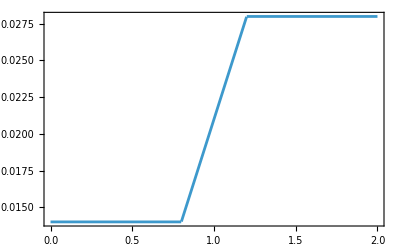

```mathematica
Plot[cd0[False,True,M],{M,0,2},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Propulsion: Thrust Lapse α

How (full) thrust varies with altitude and Mach number.

T=α Subscript[T, SLS]

### Low bypass ratio Turbofan

#### Max Power

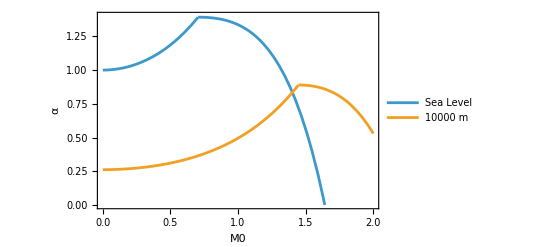

```mathematica
TRtry=1.0991599355657966(*θ0stdAVG*);
Plot[{αLTFmax[0,M0,TRtry],αLTFmax[10000,M0,TRtry]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

#### Military Power

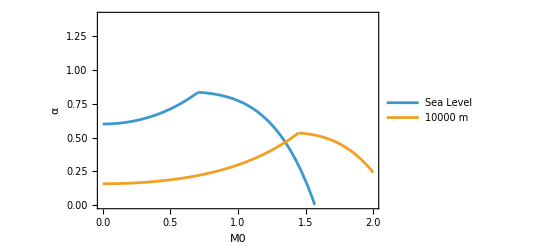

```mathematica
Plot[{αLTFmil[0,M0,TRtry],αLTFmil[10000,M0,TRtry]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Master Equation

```mathematica
RHS=β/α (q /(β WLG) (K1 ((n β)/q  WLG)^2+K2((n β)/q  WLG)+CD0+CDR)+Ps/V);
TW==RHS
```

TW==(β (Ps/V+(q (CD0+CDR+(K2 n WLG β)/q+(K1 n^2 WLG^2 β^2)/q^2))/(WLG β)))/α

### Flight Phases

#### Aircraft Settings

```mathematica
commercial=False;
If[commercial,fighter=False,fighter=True];

AR=2.4;
e=0.8;
(*Set TR as rule*)
TRValues=Range[0.8,1.4,0.01];

WGLinf=0;
WGLsup=8000;
TWRinf=0.4;
TWRsup=2.;
```

#### Mission phases 1-2: Takeoff, no obstacle

dh/dt=0
s_G assigned
C_L_max assigned 
ρ assigned
V_TO=k_TOV_Stall
T=29,8°C

```mathematica
hfield=362;
βTO=0.97064; (*β12 2nd iteration*)
g0=9.8;
Tto = 29.8+273.15;
CLmaxTO=2.;
```

```mathematica
VstallTO=Sqrt[(2* βTO*3260)/(ρfunc[hfield,Tto]*CLmaxTO)]
```

53.248

```mathematica
kTO=1.2;
VTO=kTO*Vstall/.Vstall->VstallTO;

MTO = VTO/Sqrt[γ*R*Tto]/.{γ->1.4,R->287};
Maccel =MTO/2;

(*Valore intermedio da usare per α*)
θ0TO=θ0func[T,M0]/.{T->Tto,M0->Maccel}
```

1.05313

```mathematica
ξTO=k1[commercial,fighter,Maccel,AR,e]*CL^2+cd0[commercial,fighter,Maccel]/.{CL->CLmaxTO/kTO^2};
μTO=0.05;
```

```mathematica
TWTO=(β^2/α kTO^2/(sG ρ g0 CLmax) WLG)
```

(0.146939 WLG β^2)/(CLmax sG α ρ)

```mathematica
ruleTO={
h->hfield,
T->Tto,
M0->Maccel,
β->βTO,
α->αLTFmaxFUNC[h,T,M0,TR],
sG->sTO-tr*VTO,
sTO->700,
tr->3,(*VTO->kTO*Vstall*)
(*Vstall->Sqrt[(2*WLG)/(ρ*CLmax)]*)
ρ->ρfunc[h,T],
CLmax->CLmaxTO
};
```

```mathematica
αLTFmaxFUNC[hfield,Tto,Maccel,TR]
```

Piecewise[{{0.963546, 1.05315≤TR}, {0.963546 (1-3.32335 (1.05315-TR)), 1.05315>TR}, {0, True}}]

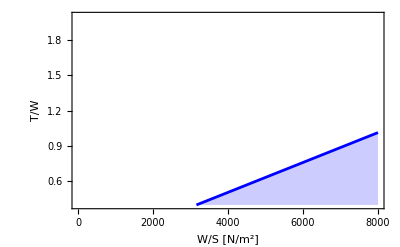

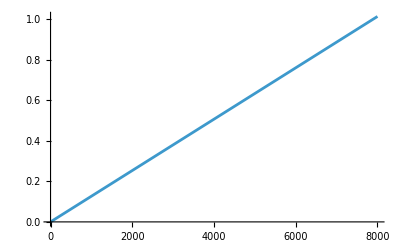

```mathematica
plotTO=Plot[TWTO//.ruleTO/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
Plot[TWTO//.ruleTO/.TR->TRtry,{WLG,0,8000}]
```

```mathematica
TWsTO=Table[TWTO//.ruleTO/.{TR->tr},{tr,TRValues}] ;(*At these conditions, α does change*)
```

```mathematica
colors=ColorData[97]/@Range[Length[TWsTO]]; (*Generates distinct colors*)

plotsTO=Table[Plot[TWsTO[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,All},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsTO]}];
```

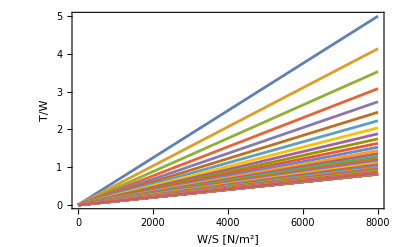

```mathematica
Show[plotsTO,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colors,TRValues,LegendLabel->"TR Values"]
```

#### Mission phases 6-7: Supersonic penetration

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power

```mathematica
βmaneuver=(20123.6-0.5*5833.24-0.5*1478.7)/20123.6 (*50% fuel, 50% armi*)
```

0.818324

```mathematica
h67=10000;
p067=pstd[h67];
M067=1.6;
β67=βmaneuver;

rule67={Ps->0,
n->1,
q->0.5 γ p067 M067^2,
M0->M067,
h->h67,
β->β67,
α->αLTFmil[h67,M067,TR],
CDR->0,
K1->k1[commercial,fighter,M067,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M067],γ->1.4};
rule67//TableForm
```

Ps→0
n→1
q→33839.3 γ
M0→1.6
h→10000
β→0.818324
α→Piecewise[{{0.666993, 1.17146≤TR}, {0.666993 (1-3.24381 (1.17146-TR)), 1.17146>TR}, {0, True}}]
CDR→0
K1→0.288
K2→0
CD0→0.028
γ→1.4

```mathematica
θ0std67=θ0std[h67,M067]
```

1.17146

```mathematica
αLTFmil[h67,M067,TR]
```

Piecewise[{{0.666993, 1.17146≤TR}, {0.666993 (1-3.24381 (1.17146-TR)), 1.17146>TR}, {0, True}}]

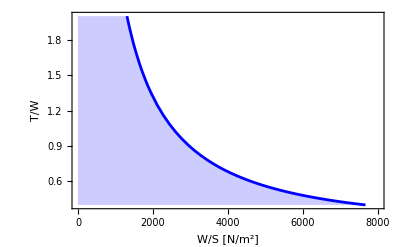

```mathematica
TW67=RHS//.rule67;
plot67=Plot[TW67/.{TR->TRtry},{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
TWs67=Table[RHS//.rule67/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(160042. (0.028+8.593×10^-11 WLG^2))/WLG,(149141. (0.028+8.593×10^-11 WLG^2))/WLG,(139631. (0.028+8.593×10^-11 WLG^2))/WLG,(131261. (0.028+8.593×10^-11 WLG^2))/WLG,(123837. (0.028+8.593×10^-11 WLG^2))/WLG,(117208. (0.028+8.593×10^-11 WLG^2))/WLG,(111253. (0.028+8.593×10^-11 WLG^2))/WLG,(105874. (0.028+8.593×10^-11 WLG^2))/WLG,(100991. (0.028+8.593×10^-11 WLG^2))/WLG,(96538.1 (0.028+8.593×10^-11 WLG^2))/WLG,(92461.6 (0.028+8.593×10^-11 WLG^2))/WLG}

```mathematica
colors=ColorData[97]/@Range[Length[TWs67]] ;(*Generates distinct colors*)

plots67=Table[Plot[TWs67[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.8,1.5}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWs67]}];
```

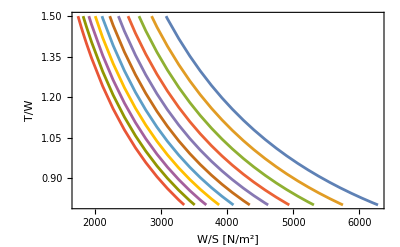

```mathematica
Show[plots67,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colors,TRValues,LegendLabel->"TR Values"]
```

#### Mission phases 7-8: Combat turn 1

dh/dt=0
dV/dt=0
n>1
h,q assigned

```mathematica
hTurn=10000;
p0Turn=pstd[hTurn];
βTurn=βmaneuver; 
MTurn1 = 1.6;

ruleTurn1={
Ps->0,
n->5,
q->0.5 γ p0Turn M0^2,
h->hTurn,
β->βTurn,
α->αLTFmax[hTurn,M0,TR],
CDR->0,
K1->k1[commercial,fighter,M0,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0],
M0->MTurn1,
γ->1.4
};
```

```mathematica
αLTFmax[hTurn,1.6,TR]/.M0->MTurn1 (*α does change with TR*)
```

Piecewise[{{1.11165, 1.17146≤TR}, {1.11165 (1-2.98772 (1.17146-TR)), 1.17146>TR}, {0, True}}]

```mathematica
θ0stdTurn1=θ0std[hTurn,M0]/.M0->MTurn1
```

1.17146

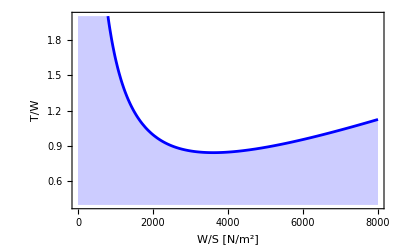

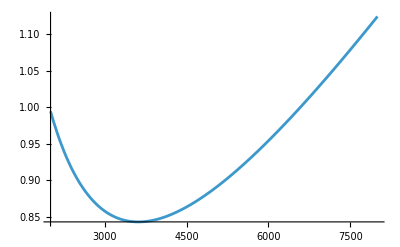

```mathematica
plotTurn1=Plot[RHS//.ruleTurn1/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
Plot[RHS//.ruleTurn1/.TR->TRtry,{WLG,2000,8000}]
```

```mathematica
TWsTurn1=Table[RHS//.ruleTurn1/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(87380. (0.028+2.14825×10^-9 WLG^2))/WLG,(82336.2 (0.028+2.14825×10^-9 WLG^2))/WLG,(77842.8 (0.028+2.14825×10^-9 WLG^2))/WLG,(73814.5 (0.028+2.14825×10^-9 WLG^2))/WLG,(70182.7 (0.028+2.14825×10^-9 WLG^2))/WLG,(66891.4 (0.028+2.14825×10^-9 WLG^2))/WLG,(63895. (0.028+2.14825×10^-9 WLG^2))/WLG,(61155.6 (0.028+2.14825×10^-9 WLG^2))/WLG,(58641.4 (0.028+2.14825×10^-9 WLG^2))/WLG,(56325.7 (0.028+2.14825×10^-9 WLG^2))/WLG,(54186. (0.028+2.14825×10^-9 WLG^2))/WLG}

```mathematica
colorsTurn1=ColorData[97]/@Range[Length[TWsTurn1]] ;(*Generates distinct colors*)

plotsTurn1=Table[Plot[TWsTurn1[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.,3}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsTurn1]}];
```

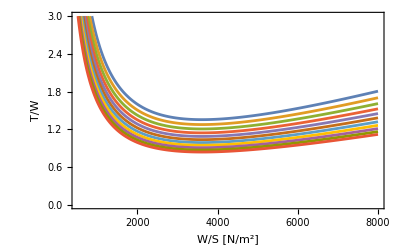

```mathematica
Show[plotsTurn1,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colorsTurn1,TRValues,LegendLabel->"TR Values"]
```

#### Mission phases 7-8: Combat turn 2

dh/dt=0
dV/dt=0
n>1
h,q assigned
same altitude and β of Combat turn 1

```mathematica
MTurn2=0.9;
```

```mathematica
ruleTurn2={
Ps->0,
n->4,
q->0.5 γ p0Turn M0^2,
h->hTurn,
β->βmaneuver,
α->αLTFmax[hTurn,M0,TR],
CDR->0,
K1->k1[commercial,fighter,M0,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0],
M0->MTurn2,
γ->1.4
};
```

```mathematica
αLTFmax[hTurn,M0,TR]/.M0->MTurn2 (*α does change with TR*)
```

Piecewise[{{0.442344, 0.900291≤TR}, {0.442344 (1-3.88763 (0.900291-TR)), 0.900291>TR}, {0, True}}]

```mathematica
θ0stdTurn2=θ0std[hTurn,M0]/.M0->MTurn2
```

0.900291

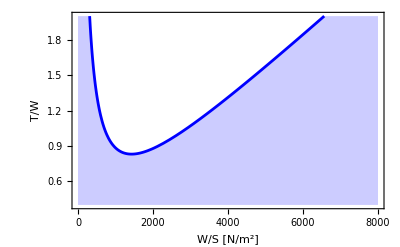

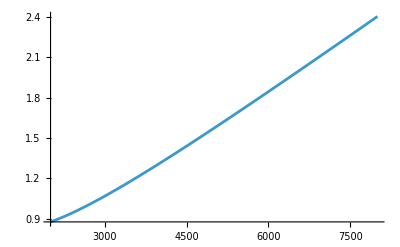

```mathematica
TWturn2=RHS//.ruleTurn2;
plotTurn2=Plot[RHS//.ruleTurn2/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
Plot[RHS//.ruleTurn2/.TR->TRtry,{WLG,2000,8000}]
```

```mathematica
TWsTurn2=Table[RHS//.ruleTurn2/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG,(33887.1 (0.0175+8.58331×10^-9 WLG^2))/WLG}

```mathematica
colorsTurn2=ColorData[97]/@Range[Length[TWsTurn2]] ;(*Generates distinct colors*)

plotsTurn2=Table[Plot[TWsTurn2[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.,3}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsTurn2]}];
```

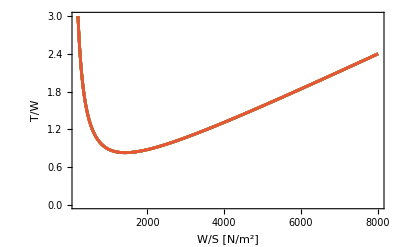

```mathematica
Show[plotsTurn2,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colorsTurn2,TRValues,LegendLabel->"TR Values"]
```

#### Mission phases 7-8: Horizontal acceleration

dh/dt=0
dV/dt assigned
n=1 (L=W)

```mathematica
g0=9.81;
h78=10000; (*si osserva che alzando la quota si alza il requisito di T/W*)
p078=pstd[h78];
M78i=0.8;
M78f=1.8;
Mavg78=(M78f+M78i)/2;
V78i=M78i*Sqrt[γ R Tstd[h78]];
V78f=M78f*Sqrt[γ R Tstd[h78]];
ΔT78=50;
dV78=(V78f-V78i)/ΔT78;
β78=βmaneuver;(*si osserva che diminuendo il peso istantaneo si abbassa il requisito di T/W*)

rule78={Ps->V*dV78/g0,
n->1,
q->0.5 γ p078 Mavg78^2,
h->h78,
β->β78,
α->αLTFmax[h78,Mavg78,TR],
CDR->0,
K1->k1[commercial,fighter,Mavg78,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg78],
M0->Mavg78,γ->1.4,R->287};
```

```mathematica
rule78//Tableform
```

Tableform[{Ps→0.030462 V √(R γ),n→1,q→22339.2 γ,h→10000,β→0.818324,α→Piecewise[{{0.724661, 1.03665≤TR}, {0.724661 (1-3.37625 (1.03665-TR)), 1.03665>TR}, {0, True}}],CDR→0,K1→0.234,K2→0,CD0→0.028,M0→1.3,γ→1.4,R→287}]

```mathematica
α->αLTFmax[h78,Mavg78,TR] (*α does change with TR*)
```

α→Piecewise[{{0.724661, 1.03665≤TR}, {0.724661 (1-3.37625 (1.03665-TR)), 1.03665>TR}, {0, True}}]

```mathematica
θ0std78=θ0std[hTurn,M0]/.M0->Mavg78
```

1.03665

(0.818324 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG))/Piecewise[{{0.724661, 1.03665≤TR}, {0.724661 (1-3.37625 (1.03665-TR)), 1.03665>TR}, {0, True}}]

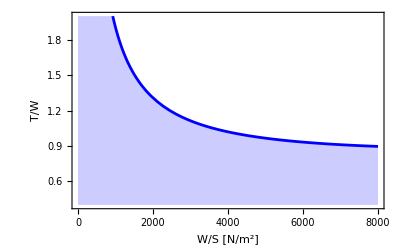

```mathematica
TW78 =RHS//.rule78
plot78=Plot[TW78/.TR->TRtry,{WLG,0,8000},Filling->Bottom,Frame->True,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
TWs78=Table[RHS//.rule78/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{1.28873 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.24091 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.19652 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.1552 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG),1.12925 (0.61061+(38218.2 (0.028+1.60205×10^-10 WLG^2))/WLG)}

```mathematica
colors78=ColorData[97]/@Range[Length[TWs78]] ;(*Generates distinct colors*)

plots78=Table[Plot[TWs78[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.5,1.5}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors78[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWs78]}];
```

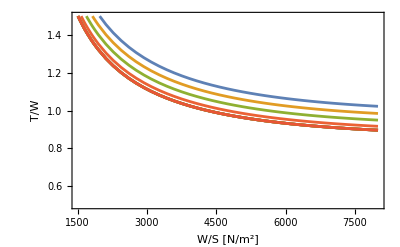

```mathematica
Show[plots78,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
TRValues2=Range[1,1.1,0.01]
```

{1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1}

```mathematica
LineLegend[colors78,TRValues2,LegendLabel->"TR Values"]
```

#### Mission phases 8-9: Escape dash

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power

```mathematica
h89=10000;
p089=pstd[h89];
M089=1.4;
β89=βmaneuver; 

rule89={Ps->0,
n->1,
q->0.5 γ p089 M089^2,
M0->M089,
h->h89,
β->β89,
α->αLTFmil[h89,M089,TR],
CDR->0,
K1->k1[commercial,fighter,M089,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M089],γ->1.4};
rule89//TableForm
```

Ps→0
n→1
q→25908.2 γ
M0→1.4
h→10000
β→0.818324
α→Piecewise[{{0.499375, 1.07849≤TR}, {0.499375 (1-3.52344 (1.07849-TR)), 1.07849>TR}, {0, True}}]
CDR→0
K1→0.252
K2→0
CD0→0.028
γ→1.4

```mathematica
θ0std89=θ0std[h89,M089]
```

1.07849

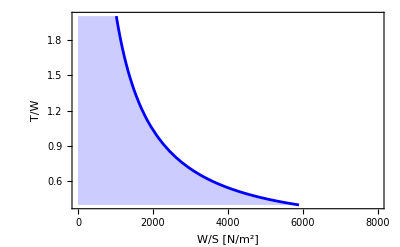

```mathematica
TW89=RHS//.rule89;
plot89=Plot[TW89/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
TWs89=Table[RHS//.rule89/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(100400. (0.028+1.28269×10^-10 WLG^2))/WLG,(95737. (0.028+1.28269×10^-10 WLG^2))/WLG,(91488.2 (0.028+1.28269×10^-10 WLG^2))/WLG,(87600.4 (0.028+1.28269×10^-10 WLG^2))/WLG,(84029.6 (0.028+1.28269×10^-10 WLG^2))/WLG,(80738.5 (0.028+1.28269×10^-10 WLG^2))/WLG,(77695.4 (0.028+1.28269×10^-10 WLG^2))/WLG,(74873.5 (0.028+1.28269×10^-10 WLG^2))/WLG,(72633.7 (0.028+1.28269×10^-10 WLG^2))/WLG,(72633.7 (0.028+1.28269×10^-10 WLG^2))/WLG,(72633.7 (0.028+1.28269×10^-10 WLG^2))/WLG}

```mathematica
colors=ColorData[97]/@Range[Length[TWs89]] ;(*Generates distinct colors*)

plots89=Table[Plot[TWs89[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.8,1.5}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWs89]}];
```

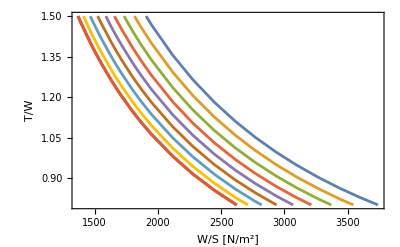

```mathematica
Show[plots89,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colors,TRValues2,LegendLabel->"TR Values"]
```

#### Mission phases 13-14: Landing, no reverse thrust

dh/dt=0
s_L assigned
C_L_max assigned 
ρ assigned
V_TD=k_TDV_Stall
α=0

```mathematica
βLanding=0.648835;
sL=700.0;
CDRc = 0.5348;
kTD=1.15;
hfield=362.;
CLmaxLanding=0.8*CLmaxTO/kTD^2
```

1.20983

```mathematica
VstallLanding=Sqrt[(2* βLanding*3260)/(ρfunc[hfield,Tto]*CLmaxLanding)]
```

55.975

```mathematica
ruleLanding={tfr->3.,
μB-> 0.18,
CL-> CLmaxLanding,
M->kTD*VstallLanding/Sqrt[γ R Tstd[hfield]],
K1->k1[commercial,fighter,M,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M],
CD->K1*CL^2+K2*CL+CD0,
ξL -> CD+CDRc-μB*CL,
β->βLanding,
α->0.,
γ->1.4,
R->287.0
};
ruleLanding//TableForm
```

tfr→3.
μB→0.18
CL→1.20983
M→3.8077/(√(R γ))
K1→Piecewise[{{0.18, M<1}, {0.18 M, M≥1}, {0, True}}]
K2→0
CD0→Piecewise[{{0.014, M≤0.8}, {-0.014+0.035 M, 0.8<M<1.2}, {0.028, M≥1.2}, {0, True}}]
CD→CD0+CL^2 K1+CL K2
ξL→0.5348+CD-CL μB
β→0.648835
α→0.
γ→1.4
R→287.

```mathematica
rulecolddensity=ρ->ρstd[hfield,-15.]
ruledensity=ρ->ρstd[hfield,0.]
rulehotdensity=ρ->ρstd[hfield,+30]
```

ρ→1.24875

ρ→1.18321

ρ→1.07081

```mathematica
WLGmax=((-b+Sqrt[b^2+4a*c])/(2a))^2//.ruledensity//.ruleLanding;
b = tfr*kTD *Sqrt[2β/(ρ* CLmaxLanding)]//.ruledensity//.ruleLanding;

a = β/(ρ*g0*ξL)*Log[1+ξL/(μB*CLmaxLanding/kTD^2)]//.ruledensity//.ruleLanding;
c = sL;
```

```mathematica
WLGmax
```

3444.19

```mathematica
pluto=ContourPlot[x==WLGmax,{x,0,8000},{y,0,8000},ContourStyle->{Green,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}];
pippo=RegionPlot[x>WLGmax,{x,0,8000},{y,0,8000},PlotStyle->LightGreen,BoundaryStyle->None];
```

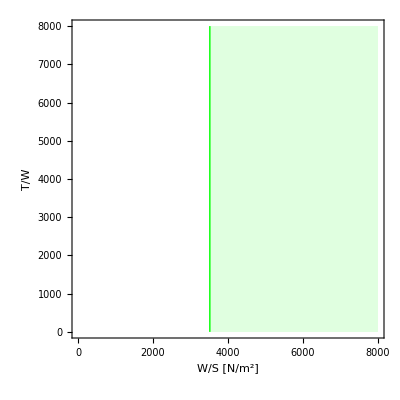

```mathematica
paperino=Show[pippo,pluto,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[
Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
WLGmaxhot=((-bhot+Sqrt[bhot^2+4ahot*chot])/(2ahot))^2//.rulehotdensity//.ruleLanding;
bhot = tfr*kTD *Sqrt[2β/(ρ* CLmaxLanding)]//.rulehotdensity//.ruleLanding;

ahot = β/(ρ*g0*ξL)*Log[1+ξL/(μB*CLmaxLanding/kTD^2)]//.rulehotdensity//.ruleLanding;
chot = sL;
```

```mathematica
WLGmaxhot
```

3181.81

```mathematica
plutohot=ContourPlot[x==WLGmaxhot,{x,0,8000},{y,0,8000},ContourStyle->{Red,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}];
pippohot=RegionPlot[x>WLGmaxhot,{x,0,8000},{y,0,8000},PlotStyle->LightRed,BoundaryStyle->None];
```

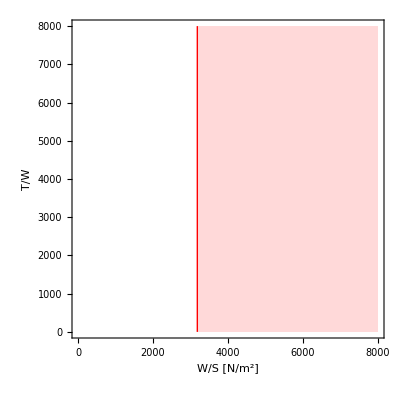

```mathematica
paperinohot=Show[pippohot,plutohot,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

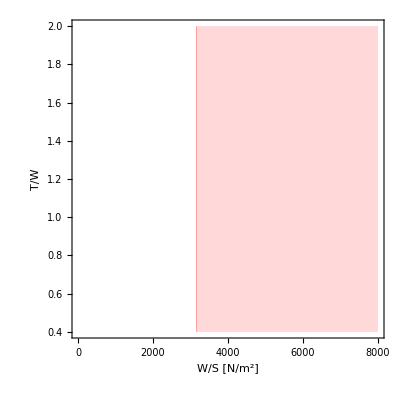

```mathematica
plotLandinghalf1=ContourPlot[x==WLGmaxhot,{x,WGLinf,WGLsup},{y,TWRinf,TWRsup},ContourStyle->{Red,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}];
plotLandinghalf2=RegionPlot[x>WLGmaxhot,{x,WGLinf,WGLsup},{y,TWRinf,TWRsup},PlotStyle->LightRed,BoundaryStyle->None];
plotLanding=Show[plotLandinghalf1,plotLandinghalf2,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
WLGmaxcold=((-bcold+Sqrt[bcold^2+4acold*ccold])/(2acold))^2//.rulecolddensity//.ruleLanding;
bcold= tfr*kTD *Sqrt[2β/(ρ* CLmaxLanding)]//.rulecolddensity//.ruleLanding;

acold = β/(ρ*g0*ξL)*Log[1+ξL/(μB*CLmaxLanding/kTD^2)]//.rulecolddensity//.ruleLanding;
ccold = sL;
```

```mathematica
WLGmaxcold
```

3710.55

```mathematica
plutocold=ContourPlot[x==WLGmaxcold,{x,0,8000},{y,0,8000},ContourStyle->{Blue,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}];
pippocold=RegionPlot[x>WLGmaxcold,{x,0,8000},{y,0,8000},PlotStyle->LightBlue,BoundaryStyle->None];
```

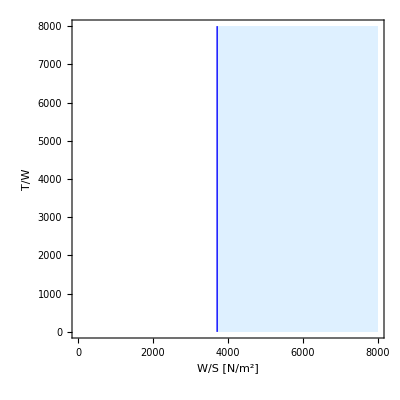

```mathematica
paperinocold=Show[pippocold,plutocold,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

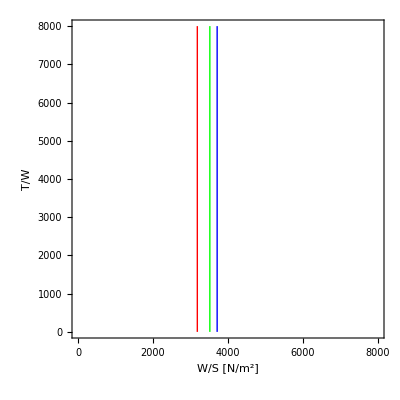

```mathematica
Show[pluto,plutocold,plutohot,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

#### Maximum Mach number @ altitude

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned

```mathematica
hmma=12192;
p0mma=pstd[hmma];
M0mma=2.;
βmma=βmaneuver;

rulemma={Ps->0,
n->1,
q->0.5 γ p0mma M0mma^2,
M0->M0mma,
h->hmma,
β->βmma,
α->αLTFmax[hmma,M0mma,TR],
CDR->0,
K1->k1[commercial,fighter,M0mma,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0mma],γ->1.4};
rulemma//TableForm
```

Ps→0
n→1
q→37380.2 γ
M0→2.
h→12192
β→0.818324
α→Piecewise[{{1.44879, 1.35336≤TR}, {1.44879 (1-2.58616 (1.35336-TR)), 1.35336>TR}, {0, True}}]
CDR→0
K1→0.36
K2→0
CD0→0.028
γ→1.4

```mathematica
α->αLTFmax[hmma,M0mma,TR]
```

α→Piecewise[{{1.44879, 1.35336≤TR}, {1.44879 (1-2.58616 (1.35336-TR)), 1.35336>TR}, {0, True}}]

```mathematica
θ0stdmma=θ0std[hmma,M0mma]
```

1.35336

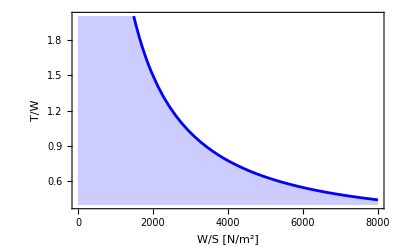

```mathematica
TWmma=RHS//.rulemma;
plotmma=Plot[TWmma/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
TWsmma=Table[RHS//.rulemma/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(419233. (0.028+8.80268×10^-11 WLG^2))/WLG,(322448. (0.028+8.80268×10^-11 WLG^2))/WLG,(261970. (0.028+8.80268×10^-11 WLG^2))/WLG,(220595. (0.028+8.80268×10^-11 WLG^2))/WLG,(190506. (0.028+8.80268×10^-11 WLG^2))/WLG,(167641. (0.028+8.80268×10^-11 WLG^2))/WLG,(149676. (0.028+8.80268×10^-11 WLG^2))/WLG,(135189. (0.028+8.80268×10^-11 WLG^2))/WLG,(123259. (0.028+8.80268×10^-11 WLG^2))/WLG,(113263. (0.028+8.80268×10^-11 WLG^2))/WLG,(104767. (0.028+8.80268×10^-11 WLG^2))/WLG}

```mathematica
colorsmma=ColorData[97]/@Range[Length[TWsmma]] ;(*Generates distinct colors*)

plotsmma=Table[Plot[TWsmma[[i]],{WLG,2000,8000},Filling->None,PlotRange->{All,{0.,3}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colorsmma[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsmma]}];
```

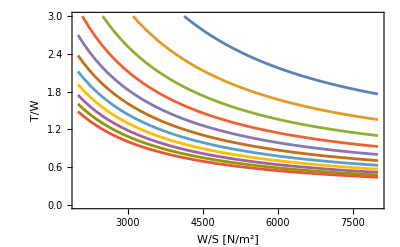

```mathematica
Show[plotsmma,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colorsmma,TRValues2,LegendLabel->"TR Values"]
```

#### Maximum Mach number @ sea level

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned

```mathematica
hmms=0.;
p0mms=pstd[hmms];
M0mms=1.25;
βmms=βmaneuver;

rulemms={Ps->0,
n->1,
q->0.5 γ p0mms M0mms^2,
M0->M0mms,
h->hmms,
β->βmms,
α->αLTFmax[hmms,M0mms,TR],
CDR->0,
K1->k1[commercial,fighter,M0mms,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0mms],γ->1.4};
rulemms//TableForm
```

Ps→0
n→1
q→79160.2 γ
M0→1.25
h→0.
β→0.818324
α→Piecewise[{{2.59029, 1.3125≤TR}, {2.59029 (1-2.66667 (1.3125-TR)), 1.3125>TR}, {0, True}}]
CDR→0
K1→0.225
K2→0
CD0→0.028
γ→1.4

```mathematica
θ0stdmms=θ0std[hmms,M0mms]
```

1.3125

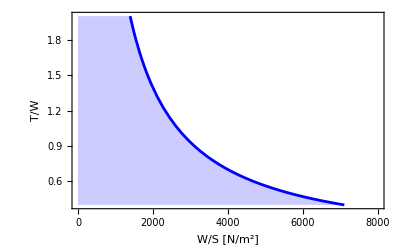

```mathematica
TWmms=RHS//.rulemms;
plotmms=Plot[TWmms/.TR->TRtry,{WLG,0,8000},Filling->Bottom,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
TWsmms=Table[RHS//.rulemms/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{(256707. (0.028+1.22677×10^-11 WLG^2))/WLG,(221299. (0.028+1.22677×10^-11 WLG^2))/WLG,(194475. (0.028+1.22677×10^-11 WLG^2))/WLG,(173451. (0.028+1.22677×10^-11 WLG^2))/WLG,(156529. (0.028+1.22677×10^-11 WLG^2))/WLG,(142615. (0.028+1.22677×10^-11 WLG^2))/WLG,(130973. (0.028+1.22677×10^-11 WLG^2))/WLG,(121088. (0.028+1.22677×10^-11 WLG^2))/WLG,(112591. (0.028+1.22677×10^-11 WLG^2))/WLG,(105208. (0.028+1.22677×10^-11 WLG^2))/WLG,(98733.6 (0.028+1.22677×10^-11 WLG^2))/WLG}

```mathematica
colorsmms=ColorData[97]/@Range[Length[TWsmms]] ;(*Generates distinct colors*)

plotsmms=Table[Plot[TWsmms[[i]],{WLG,2000,8000},Filling->None,PlotRange->{All,{0.,3}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsmms]}];
```

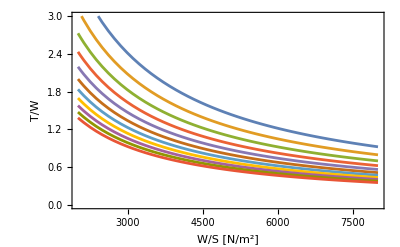

```mathematica
Show[plotsmms,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colorsmms,TRValues2,LegendLabel->"TR Values"]
```

#### Super-cruise @ altitude

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power 
weight after take off, i.e. β = 0.95

```mathematica
hScrz=12192; (*40 kft*)
p0Scrz=pstd[hScrz];
M0Scrz=1.5;
βScrz=βmaneuver; (*Si è osservato che β influisce poco poiché modifica solo il coefficiente di WGL^2 che è comunque dell'ordine di 10^(-10)*)
```

```mathematica
θ0stdScrz=θ0std[hScrz,M0Scrz]
```

1.0902

```mathematica
ruleScrz={Ps->0,
n->1,
q->0.5 γ p0Scrz M0Scrz^2,
h->hScrz,
β->βScrz,
α->αLTFmil[hScrz,M0Scrz,TR],
CDR->0,
K1->k1[commercial,fighter,M0Scrz,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0Scrz],γ->1.4};
ruleScrz//TableForm
```

Ps→0
n→1
q→21026.3 γ
h→12192
β→0.818324
α→Piecewise[{{0.407841, 1.0902≤TR}, {0.407841 (1-3.48558 (1.0902-TR)), 1.0902>TR}, {0, True}}]
CDR→0
K1→0.27
K2→0
CD0→0.028
γ→1.4

```mathematica
αLTFmil[hScrz,M0Scrz,TR]
```

Piecewise[{{0.407841, 1.0902≤TR}, {0.407841 (1-3.48558 (1.0902-TR)), 1.0902>TR}, {0, True}}]

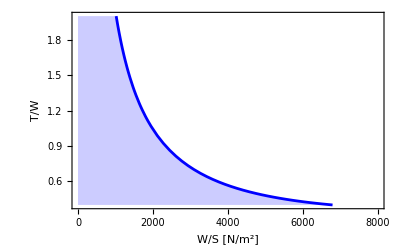

```mathematica
plotScrz=Plot[RHS//.ruleScrz/.{TR->TRtry},{WLG,0,8000},Filling->Bottom,PlotStyle->{Blue},PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
(*TRValues=Range[1,1.1,0.01];
TWsScrz={};  (*Empty list*)
For[i=1,i<=Length[TRValues],i++,AppendTo[TWsScrz,RHS//.ruleScrz/.TR->TRValues[[i]]]]*)
```

```mathematica
TWsScrz=Table[RHS//.ruleScrz/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does not change*)
```

{(105279. (0.028+2.08656×10^-10 WLG^2))/WLG,(100185. (0.028+2.08656×10^-10 WLG^2))/WLG,(95561.7 (0.028+2.08656×10^-10 WLG^2))/WLG,(91346.2 (0.028+2.08656×10^-10 WLG^2))/WLG,(87486.9 (0.028+2.08656×10^-10 WLG^2))/WLG,(83940.5 (0.028+2.08656×10^-10 WLG^2))/WLG,(80670.4 (0.028+2.08656×10^-10 WLG^2))/WLG,(77645.6 (0.028+2.08656×10^-10 WLG^2))/WLG,(74839.3 (0.028+2.08656×10^-10 WLG^2))/WLG,(72228.9 (0.028+2.08656×10^-10 WLG^2))/WLG,(72177.3 (0.028+2.08656×10^-10 WLG^2))/WLG}

```mathematica
colorsScrz=ColorData[97]/@Range[Length[TWsScrz]]; (*Generates distinct colors*)

plotsScrz=Table[Plot[TWsScrz[[i]],{WLG,2000,8000},PlotRange->{All,{0.,1.34}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colors[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsScrz]}];
```

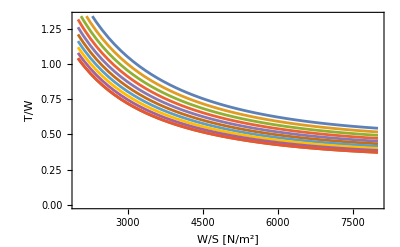

```mathematica
Show[plotsScrz,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

#### Acceleration @ sea level

dh/dt=0
dV/dt assigned
n=1 (L=W)

```mathematica
g0=9.81;
hAcc=0; (*si osserva che alzando la quota si alza il requisito di T/W*)
p0Acc=pstd[hAcc];
MAcc1=0.3;
MAcc2=1.0;
Mavg=(MAcc2+MAcc1)/2; (*da cambiare nome*)
VAcc1=MAcc1*Sqrt[γ R Tstd[hAcc]];
VAcc2=MAcc2*Sqrt[γ R Tstd[hAcc]];
ΔT=30;
dV=(VAcc2-VAcc1)/ΔT;
βAcc=0.95;(*si osserva che diminuendo il peso istantaneo si abbassa il requisito di T/W*)

ruleAcc={Ps->V*dV/g0,
n->1,
q->0.5 γ p0Acc Mavg^2,
h->hTurn,
β->βAcc,
α->αLTFmax[hAcc,Mavg,TR],
CDR->0,
K1->k1[commercial,fighter,Mavg,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg],
M0->Mavg,γ->1.4,R->287};
```

```mathematica
ruleAcc//Tableform
```

Tableform[{Ps→0.0403754 V √(R γ),n→1,q→21404.9 γ,h→10000,β→0.95,α→Piecewise[{{1.32832, 1.0845≤TR}, {1.32832 (1-3.22729 (1.0845-TR)), 1.0845>TR}, {0, True}}],CDR→0,K1→0.18,K2→0,CD0→0.014,M0→0.65,γ→1.4,R→287}]

```mathematica
α->αLTFmax[hAcc,Mavg,TR] (*α does change with TR*)
```

α→Piecewise[{{1.32832, 1.0845≤TR}, {1.32832 (1-3.22729 (1.0845-TR)), 1.0845>TR}, {0, True}}]

```mathematica
θ0stdAcc=θ0std[hAcc,Mavg]
```

1.0845

(0.95 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG))/Piecewise[{{1.32832, 1.0845≤TR}, {1.32832 (1-3.22729 (1.0845-TR)), 1.0845>TR}, {0, True}}]

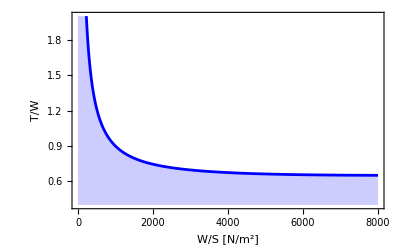

```mathematica
TWAcc =RHS//.ruleAcc
plotAcc=Plot[TWAcc/.TR->TRtry,{WLG,0,8000},Filling->Bottom,Frame->True,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
TWsAcc=Table[RHS//.ruleAcc/.{TR->tr},{tr,1,1.1,0.01}] (*At these conditions, α does change*)
```

{0.983355 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.941574 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.903198 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.867828 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.835124 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.804795 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.776592 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.750299 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.725728 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.715188 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG),0.715188 (0.809323+(31544.1 (0.014+1.80899×10^-10 WLG^2))/WLG)}

```mathematica
colorsAcc=ColorData[97]/@Range[Length[TWsAcc]] ;(*Generates distinct colors*)

plotsAcc=Table[Plot[TWsAcc[[i]],{WLG,0,8000},Filling->None,PlotRange->{All,{0.5,1.5}},Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotStyle->{colorsAcc[[i]]},(*Assign different colors*)FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]],{i,1,Length[TWsAcc]}];
```

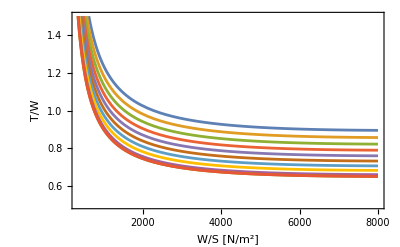

```mathematica
Show[plotsAcc,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

```mathematica
LineLegend[colorsAcc,TRValues2,LegendLabel->"TR Values"]
```

#### Service Ceiling

The maximum altitude at which the aircraft can cruise still having 100ft/min of remaining climb rate. The aircraft has to fly at its maximum efficiency attitude (C_L= √(C_D_0 π AR e)) and full thrust

dV/dt=0
n=1 (L=W)
C_L assigned -> maximum efficiency C_L
h assigned
dh/dt assigned -> 2.5 m/s = 500 ft/min (it’s a jet aircraft)

```mathematica
ht=2.5;
hCeil=16764;
p0Ceil=pstd[hCeil];
βCeil=0.699331; (*after the climb post combat, β78 da 2nd iteration*)
M0Crit=0.8;
CLe=Sqrt[cd0[commercial,fighter,M0Crit]*Pi AR e]
```

0.290596

```mathematica
ruleCeil={Ps->ht,
n->1,
q->0.5 γ p0Ceil M0Crit^2,
h->hCeil,
β->βCeil,
α->αLTFmax[hCeil,M0Crit,TR],
CDR->0,
K1->k1[commercial,fighter,M0Crit,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0Ceil],
V->Sqrt[2 β WLG /( ρstd[hCeil,0] CLe)],
M0Ceil->V/Sqrt[γ R Tstd[hCeil]],γ->1.4,R->287.};
```

```mathematica
α->αLTFmax[hCeil,M0Crit,TR] (*α does not change with TR*)
```

α→Piecewise[{{0.12658, 0.848104≤TR}, {0.12658 (1-4.12685 (0.848104-TR)), 0.848104>TR}, {0, True}}]

```mathematica
θ0stdCeil=θ0std[hCeil,M0Crit]
```

0.848104

```mathematica
TWceil =RHS//.ruleCeil;
```

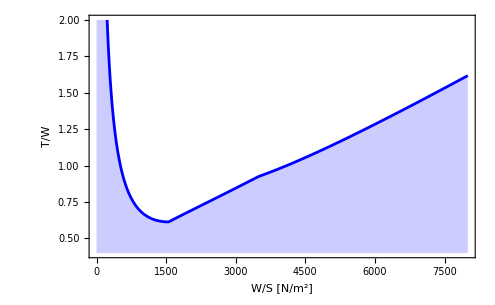

```mathematica
plotCeil=Plot[TWceil/.TR->TRtry,{WLG,0,8000},Filling->Bottom,Frame->True,PlotRange->{{WGLinf,WGLsup},{TWRinf,TWRsup}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Instantaneous Turn Rate

C_L_max assigned =1.5
V_C=420 kts (EAS)
dψ/dt= 30 deg/s

```mathematica
βmaneuver
```

0.818324

```mathematica
ruleITR={dψ->30*Pi/180,
Vc->216,(*m/s*)
q->0.5*ρstd[0.,0.]*Vc^2,
CLmax->1.5,
β->βmaneuver,
n->Sqrt[(dψ*Vc/g)^2+1],
g->9.81
};
ruleITR//TableForm
```

dψ→π/6
Vc→216
q→0.612613 Vc^2
CLmax→1.5
β→0.818324
n→√(1+(dψ^2 Vc^2)/g^2)
g→9.81

```mathematica
WLGmaxITR=q*CLmax/(β*n)//.ruleITR
```

4527.4

```mathematica
plotITRhalf1=ContourPlot[x==WLGmaxITR,{x,0,8000},{y,0,8000},ContourStyle->{Green,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}];
plotITRhalf2=RegionPlot[x>WLGmaxITR,{x,0,8000},{y,0,8000},PlotStyle->LightGreen,BoundaryStyle->None];
```

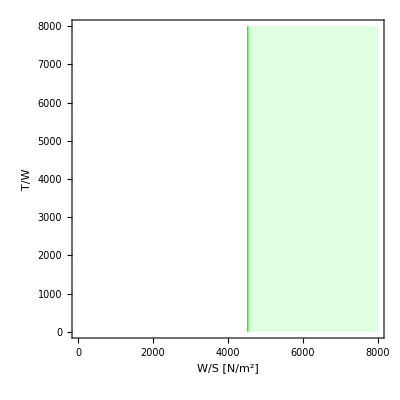

```mathematica
plotITR=Show[plotITRhalf1,plotITRhalf2,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[
Black,FontSize->16,FontFamily->"Arial"]]
```

### Constraint Diagram

The solution space is the white region over the constraint curves

```mathematica
θ0stdVEC={θ0std67,θ0std78,θ0std89,θ0stdTurn1,θ0stdTurn2,θ0stdmma,θ0stdmms,θ0stdScrz,θ0stdCeil,θ0stdScrz,θ0stdAcc,θ0TO}
```

{1.17146,1.03665,1.07849,1.17146,0.900291,1.35336,1.3125,1.0902,0.848104,1.0902,1.0845,1.05313}

```mathematica
θ0stdAVG = Mean[θ0stdVEC](*il TR dovrebbe essere la media dei range di θ0std, per cui CAMBIA TRtry con questo valore*)
```

1.0992

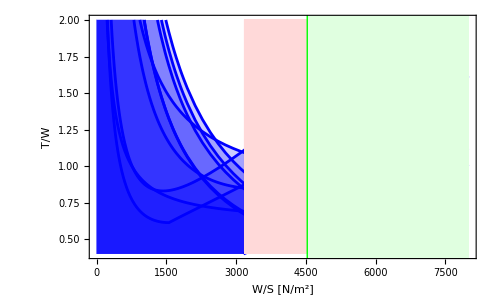

```mathematica
ConstraintFullPlot1=Show[plotTurn1,plotTurn2,plotTO,plotmma,plotmms,plot67,plot78,plot89,plotCeil,plotAcc,plotScrz,plotLanding,plotITR,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"}]
```

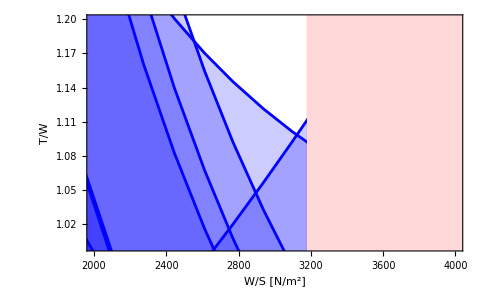

```mathematica
ConstraintFullPlotZoom1=Show[plotTurn1,plotTurn2,plotTO,plotmma,plotmms,plot67,plot78,plot89,plotCeil,plotAcc,plotScrz,plotITR,plotLanding,Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotRange->{{2000,4000},{1.0,1.2}}]
```

```mathematica
TWratio=1.11;
WLGTO=3100.;
Print[Style["Aircraft characteristic ratios",20,Bold,Red]];
	Print[TableForm[
	{TWratio,WLGTO},
	TableHeadings->{{"Take-Off-Thrust-to-MTOW ratio (T/W) ","Wing loading (W/S) "},None}
	]
];
```

Aircraft characteristic ratios

Take-Off-Thrust-to-MTOW ratio (T/W)  | 1.11
Wing loading (W/S)  | 3100.

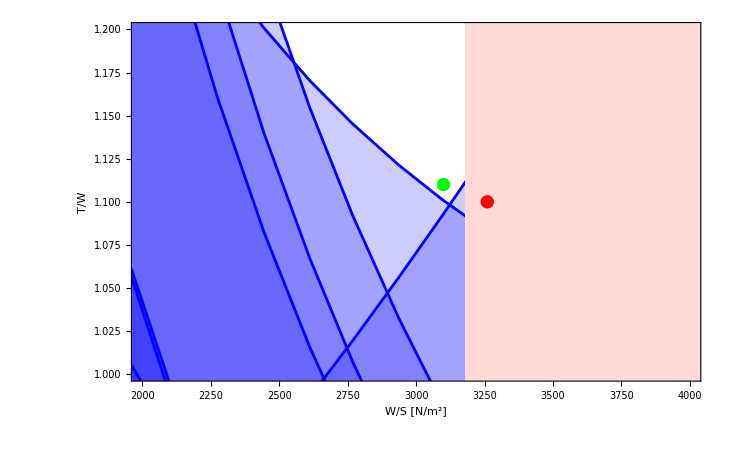

```mathematica
pointproject1st=ListPlot[{{3260,1.10}},PlotStyle->Red];
pointproject2st=ListPlot[{{3100,1.11}},PlotStyle->Green];
pointproject3rd=ListPlot[{{WLGTO,TWratio}},PlotStyle->Green];
Show[ConstraintFullPlot1,pointproject1st,pointproject2st, Frame->True,FrameLabel->{"\!\(\*FractionBox[\(W\), \(S\)]\) [N/\!\(\*SuperscriptBox[\(m\), \(2\)]\)]","\!\(\*FractionBox[\(T\), \(W\)]\)"},PlotRange->{{2000,4000},{1.0,1.2}}]
```

### Constant PS contours

V(T-D)/W=(d(V^2/(2 g_0)+h))/dt=dz_e/dt=P_S

where z_e represents the aircraft mechanical energy (kinetic + potential) and is often referred to as “energy height”. P_S is the time rate of change of the energy height and is called weight specific excess power.

Once T/W and W/S are selected, it is possible to compute the weight specific excess power for flight at any chosen β, n, altitude, and velocity. Fighter pilots routinely compare these Ps diagrams for their aircraft with those of their potential adversaries in order to determine where in the flight envelope they enjoy the greatest combat advantage.

```mathematica
rulePS1={n->1,
β->0.97,
α->αLTFmilh1[h,M0,TRtry],
TW->TWratio,
WLG->WLGTO,
K1->k1[commercial,fighter,M0,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0],
q->0.5 ρstd1[h,0]V^2,
M0->(V/Sqrt[γ R Tstd1[h]]),
γ->1.4,R->287};
```

```mathematica
rulePS2={n->1,
β->0.97,
α->αLTFmilh2[h,M0,TRtry],
TW->TWratio,
WLG->WLGTO,
K1->k1[commercial,fighter,M0,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0],
q->0.5 ρstd2[h,0]V^2,
M0->(V/Sqrt[γ R Tstd2[h]]),
γ->1.4,R->287};
```

```mathematica
rulePS3={n->1,
β->0.97,
α->αLTFmilh3[h,M0,TRtry],
TW->TWratio,
WLG->WLGTO,
K1->k1[commercial,fighter,M0,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0],
q->0.5 ρstd3[h,0]V^2,
M0->(V/Sqrt[γ R Tstd3[h]]),
γ->1.4,R->287};
```

```mathematica
zEBCA=h+(V^2)/(2*g0)//.{h->BCAinit,V->0.8*Sqrt[γ*R*Tstd1[h]],γ->1.4,R->287};
solutionsFINALCLIMB=Solve[BCAinit+V^2/(2*9.81)==zEBCA,V];
positiveRootFINALCLIMB=V/. Select[solutionsFINALCLIMB,(V/. #)>0&][[1]];
VfinalClimb=positiveRootFINALCLIMB;
Print["zEBCA: ",zEBCA]
Print["VfinalClimb: ",VfinalClimb]
```

zEBCA: 13629.3

VfinalClimb: 236.917

```mathematica
hMid3=8500;
hFin2=6300;(*modificata*)
```

```mathematica
solutionshmid3=Solve[hMid3+V^2/(2*9.81)==zEBCA,V];
positiveRoothmid3=V/. Select[solutionshmid3,(V/. #)>0&][[1]];
vMid3=positiveRoothmid3
```

317.233

```mathematica
solutionshfin2=Solve[hFin2+V^2/(2*9.81)==zEBCA,V];
positiveRoothfin2=V/. Select[solutionshfin2,(V/. #)>0&][[1]];
vFin2=positiveRoothfin2
```

379.211

```mathematica
hin1 =hfield;
hmid1=2700;
hfin1=4300;
vin1=Vclimb;
vmid1=305;
vfin1=340;
Min1=Mclimb;
Mmid1=vmid1/Sqrt[γ*R*Tstd[hmid1]]/.{γ->1.4,R->287};
Mfin1=vfin1/Sqrt[γ*R*Tstd[hfin1]]/.{γ->1.4,R->287};

hin2=hfin1;
hmid2=5150;
hfin2=hFin2;
vin2=vfin1;
vmid2=355;
vfin2=vFin2;
Min2=Mfin1;
Mmid2=vmid2/Sqrt[γ*R*Tstd[hmid2]]/.{γ->1.4,R->287};
Mfin2=vfin2/Sqrt[γ*R*Tstd[hfin2]]/.{γ->1.4,R->287};

hin3=hfin2;
hmid3=hMid3;
hfin3=BCAinit;
vin3=vfin2;
vmid3=vMid3;
vfin3=VfinalClimb;
Min3=Mfin2;
Mmid3=vmid3/Sqrt[γ*R*Tstd[hmid3]]/.{γ->1.4,R->287};
Mfin3=vfin3/Sqrt[γ*R*Tstd[hfin3]]/.{γ->1.4,R->287};
```

```mathematica
(*Nomi delle variabili*)punti={"hin1","hmid1","hfin1","hin2","hmid2","hfin2","hin3","hmid3","hfin3"};

velocità={"vin1","vmid1","vfin1","vin2","vmid2","vfin2","vin3","vmid3","vfin3"};

mach={"Min1","Mmid1","Mfin1","Min2","Mmid2","Mfin2","Min3","Mmid3","Mfin3"};
(*Definizione dei gruppi*)colori={LightBlue,LightGray,White};

(*Tabella con valori numerici arrotondati*)
tabella=Table[Module[{nome=punti[[i]],h=N[ToExpression[punti[[i]]],4],v=N[ToExpression[velocità[[i]]],4],m=N[ToExpression[mach[[i]]],4]},{nome,h,v,m}],{i,Length[punti]}];

(*Funzione per assegnare il colore di riga ogni 3 righe*)
righeColorate=MapIndexed[Prepend[#1,colori[[Quotient[#2[[1]]-1,3]+1]]]&,tabella];

(*Grid con intestazione e sfondo a colori*)
ClimbSchedule=Grid[Prepend[righeColorate,{None,"Punto","Altezza h [m]","Velocità V [m/s]","Mach"}],Frame->All,Alignment->Left,Background->{Automatic}]
```

None | Punto | Altezza h [m] | Velocità V [m/s] | Mach
RGBColor[0.87, 0.94, 1] | hin1 | 362. | 270. | 0.773879
RGBColor[0.87, 0.94, 1] | hmid1 | 2700. | 305. | 0.924964
RGBColor[0.87, 0.94, 1] | hfin1 | 4300. | 340. | 1.05149
GrayLevel[0.85] | hin2 | 4300. | 340. | 1.05149
GrayLevel[0.85] | hmid2 | 5150. | 355. | 1.1097
GrayLevel[0.85] | hfin2 | 6300. | 379.211 | 1.20314
GrayLevel[1] | hin3 | 6300. | 379.211 | 1.20314
GrayLevel[1] | hmid3 | 8500. | 317.233 | 1.03686
GrayLevel[1] | hfin3 | 10768.5 | 236.917 | 0.8

```mathematica
(*Colori per i segmenti*)coloriSegmenti={Red,Yellow,Blue};

(*Lista dei punti (V,h)*)
puntiVH=Table[{N[ToExpression[velocità[[i]]],4],(*x:velocità*)N[ToExpression[punti[[i]]],4]      (*y:quota*)},{i,Length[punti]}];

(*Etichette da mostrare*)
etichette=punti;

(*Segmenti divisi in 3 gruppi da 3*)
segmenti=Partition[puntiVH,3,3];

(*Grafica delle spezzate a colori*)
spezzateGrafica=Table[{Thick,coloriSegmenti[[i]],Line[segmenti[[i]]]},{i,Length[segmenti]}];

(*Etichette grafiche*)
etichetteGrafica=Table[Text[Style[etichette[[i]],12,Bold],puntiVH[[i]],{1,-1}],{i,Length[puntiVH]}];

(*-->Questo è l'oggetto grafico che puoi usare dentro Show[]*)
graficoClimb=Graphics[{spezzateGrafica,PointSize[Medium],Black,Point/@puntiVH,etichetteGrafica}];
```

```mathematica
point1=ListPlot[{{Vclimb,hfield}},PlotStyle->Red];
line1=ListPlot[{{0,362},{Vclimb,hfield}},Joined->True,PlotStyle->{Dashed,Red}];
line2=ListPlot[{{Vclimb,0},{Vclimb,hfield}},Joined->True,PlotStyle->{Dashed,Red}];
line3=ListPlot[{{0,0},{Vclimb,hfield}},Joined->True,PlotStyle->{Dashed,Blue}];
line4=ListPlot[{{0,BCAinit},{600,BCAinit}},Joined->True,PlotStyle->{Dashed,Red}];
line5=ListPlot[{{VfinalClimb,0},{VfinalClimb,20000}},Joined->True,PlotStyle->{Dashed,Green}];
point2=ListPlot[{{VfinalClimb,BCAinit}},PlotStyle->Red];
```

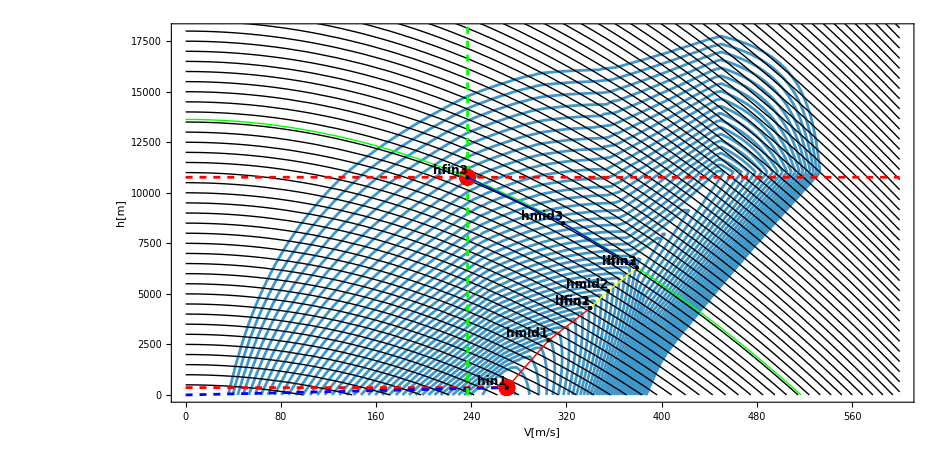

```mathematica
Show[
Table[
ContourPlot[
Evaluate[V(α/β TW-K1 n^2 β/q WLG - K2 n - CD0/(β WLG/q))==cost//.rulePS1],
{V,0,600},{h,0,11000},
AspectRatio->0.5,
ContourLabels->None,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"V[m/s]","h[m]"},
Exclusions->None],   
{cost,0,600,5}],
Table[
ContourPlot[h+V^2/(2*9.81)==c1,{V,0,600},{h,0,11000},
ContourStyle->{Black,Thin},
ContourLabels->None],
{c1,0,38000,500}],
Table[
ContourPlot[
Evaluate[V(α/β TW-K1 n^2 β/q WLG - K2 n - CD0/(β WLG/q))==cost//.rulePS2],
{V,0,600},{h,11000,20000},
AspectRatio->0.5,
ContourLabels->None,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"V[m/s]","h[m]"},
Exclusions->None],
{cost,0,600,5}],
Table[
ContourPlot[h+V^2/(2*9.81)==c1,{V,0,600},{h,11000,20000},
ContourStyle->{Black,Thin},
ContourLabels->None],
{c1,0,38000,500}],
point1,
line1,
line2,
line3,
line4,
line5,
point2,
ContourPlot[h+V^2/(2*9.81)==zEBCA,{V,0,600},{h,0,20000},
ContourStyle->{Green,Thick},
ContourLabels->None],
graficoClimb,
PlotRange->{{0,600},{0,18000}}

]
```

## Mission Analysis

### Thrust Specific Fuel Consumption (TSFC) Constants

```mathematica
C1mil=0.9;
C2mil=0.3;
C1max=1.6;
C2max=0.27;
```

### Result From Constrain Analysis

```mathematica
WTratio=1/TWratio
SWratio=1/WLGTO
```

0.900901

0.000322581

### Mission Phase

#### 1-2: Warm-Up and Take-Off

##### A) Warm - Up Phase

dV/dt=0, dh/dt=0
M=0,  D=0,  R=T=αT_SL
h=362m ASL 
T=29,8°C
Δt=60s , mil power

```mathematica
CalculateΠA[h_,M_,TR_,βi_,Δt_,θ_,T_]:=Module[
{α,ΠA, βA},
α=αLTFmilFUNC[h,T,M,TR];
ΠA=1-(C1mil/(3600 Sqrt[θ])*(α/βi)*TWratio*Δt);
βA=βi*ΠA;
Return[{ΠA,βA}];
]
ruleWarmUp={
h->hfield,
M->0.,
TR->TRtry,
βi->βTO,
Δt->60,
θ->θfunc[T],
T->Tto
};
paramsA= {h,M,TR,βi,Δt,θ,T}//.ruleWarmUp;
```

```mathematica
{Π12A,β12A}=CalculateΠA@@paramsA
```

{0.990386,0.961308}

##### B) Take-Off Acceleration

dh/dt=0
h=362m ASL
T=29,8°C
k_TO=1.2, μ_TO=0.05, CL_max=2, 
M_accel=M_TO/2
max power

```mathematica
CalculateΠB[h_,M_,TR_,T_,βi_,θ_]:=Module[
{q,TSFC,u,ΠB,βB},
q=(ρfunc[h,T]*VTO^2)/2;
TSFC=(C1max+C2max*M) Sqrt[θ];
u=(ξTO*(q/βi)*(SWratio)+μTO)*(βi/αLTFmaxFUNC[h,T,M,TR])*(WTratio);
ΠB=Exp[(-(TSFC/3600) Sqrt[θ]/g0)*(VTO/(1-u))];
βB =βi*ΠB;
Return [{ΠB,βB}]
]
paramsB={h,M,TR,T,βi,θ}//.ruleTakeOffAcc;
ruleTakeOffAcc={
h->hfield,
M->Maccel,
TR->TRtry,
βi->β12A,
θ->θfunc[T],
T->Tto
};
```

ReplaceRepeated::reps: {ruleTakeOffAcc} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
{Π12B,β12B}=CalculateΠB@@paramsB
```

{0.995637,0.957114}

##### C) Take-Off Rotation

dV/dt=0, dh/dt=0
h=609,6m ASL = 2000 ASL , T=29,8°C
t_R=3s , max power (α_wet), M_TO

```mathematica
CalculateΠC[h_,T_,M_,TR_,θ_,βi_,tR_]:=Module[
{α,TSFC,ΠC,βC},
α=αLTFmaxFUNC[h,T,M,TR];
TSFC=(C1max+C2max*M) Sqrt[θ];
ΠC=1-(TSFC/3600)*(α/βi)*(TWratio) *tR;
βC =βi*ΠC;
Return[{ΠC,βC}];
]

ruleTakeOffRotation={
h->hfield,
M->MTO,
TR->TRtry,
βi->βTO*Π12A*Π12B,
θ->θfunc[T],
T->Tto,
tR->3
};
paramsC={h,T,M,TR,θ,βi,tR}//.ruleTakeOffRotation;
```

```mathematica
ruleTakeOffRotation//TableForm
```

h→362.
M→0.183145
TR→1.09916
βi→0.957114
θ→0.00347041 T
T→302.95
tR→3

```mathematica
{Π12C,β12C}=CalculateΠC@@paramsC
```

{0.998397,0.95558}

##### Overall Weight Fraction 1-2

```mathematica
Calculateβ12[βin_]:=Module[
{ΠA,ΠB,ΠC,Π12,β12},
ΠA=(CalculateΠA@@paramsA)[[1]];
ΠB=(CalculateΠB@@paramsB)[[1]];
ΠC=(CalculateΠC@@paramsC)[[1]];
Π12=ΠA*ΠB*ΠC;
β12=βin*Π12;
Print["ΠA = ",ΠA];
Print["ΠB = ",ΠB];
Print["ΠC = ",ΠC];
Print["Π12 = ",Π12];
Print["β12 = ",β12];
Return[{Π12,β12}];
];
```

```mathematica
{Π12,β12}=Calculateβ12[βTO]
```

ΠA = 0.990386

ΠB = 0.995637

ΠC = 0.998397

Π12 = 0.984484

β12 = 0.95558

{0.984484,0.95558}

ΠB = 0.996535

ΠC = 0.998475

Π12 = 0.985814

β12 = 0.985814

0.985814

ΠB = 0.996535

ΠC = 0.998475

Π12 = 0.985814

β12 = 0.985814

0.985814

#### Mission Phase 2-3: Accelerate and Climb

##### D) Horizontal Acceleration

dh/dt=0
n=1, L=W, Mach valore medio tra M_TO e M_CL
h_initial=2000 ft, h_final=2000 ft ft
mil power

```mathematica
Vclimb=270; (*visto a occhio dal grafico PS contour*);
```

```mathematica
Mclimb=Vclimb/Sqrt[γ*R*Tto]/.{γ->1.4,R->287}
```

0.773879

```mathematica
MavgD=(MTO+Mclimb)/2
```

0.478512

```mathematica
CalculateΠD[h_,T_,M_,TR_,ΔEpot_,Vi_,Vf_,βi_,δ_]:=Module[
{α,ΔEcin,Δz,CL,CD,CDCL,u,C1MC2,ΠD,βD,V,TΔSW,Δt,Δs},
α=αLTFmilFUNC[h,T,M,TR];
ΔEcin=(Vf^2-Vi^2)/(2*g0)//.({g0-> 9.81});
Δz=ΔEpot+ΔEcin;
CL=(2 βi*(WLG))/(γ*presstd*δ*M^2)//.{presstd->101325,γ->1.4,WLG->WLGTO};
CD=k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M];
CDCL=CD/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1mil/M)+C2mil;
ΠD=Exp[-(C1MC2/(astd*3600))*(Δz/(1-u))]//.{astd->340.3};
βD=βi*ΠD;
V=M*Sqrt[γ*R*T]/.{γ->1.4,R->287};
TΔSW=Δz/(1-u);
Δt=TΔSW*(1/V)*(βi/α)*(WTratio);
Δs=V*Δt;
Return[{ΠD,βD,Δt,Δs}];
]
ruleHorizAccel={
h->hfield,
M->MavgD,
TR->TRtry,
ΔEpot->0.,
Vi->VTO,
Vf->Vclimb,
βi->β12,
θ->θfunc[T],
T->Tto,
δ->δstd[h]
};
paramsD={h,T,M,TR,ΔEpot,Vi,Vf,βi,δ}//.ruleHorizAccel;

{Π23D,β23D,ΔtD,ΔsD}=CalculateΠD@@paramsD
```

{0.992781,0.948681,31.2598,5218.78}

##### E) Climb and Acceleration

n=1, L=W, T_in=29,8°C
mil power

Best Subsonic Cruise Altitude

-Graphics-

Initial BCA

```mathematica
βinit=β23D;
WLT0=WLGTO;
```

```mathematica
δinit=((2β)/(γ pstd[0] M0^2))(1/(√((CD0+CDR)/K1)))WLT0//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],M0->0.8,β->βinit,γ->1.4}
```

0.232306

```mathematica
Quiet[BCAinit=h/.Solve[Reduce[δstd[h]==δinit],h][[1]]]
```

10768.5

```mathematica
(*delta=δinit;*)
```

```mathematica
(*Solve[delta==((2β)/(γa p0 M0^2))(1/(√((CD0+CDR)/K1)))WLG//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],M0->0.8,γ->1.4,WLG->WLT0},β]*)
```

```mathematica
(*RUNNARE FINO A QUI PRIMA DEL CONTOUR PS per il CLIMB SCHEDULE*)
```

```mathematica
CalculateΠclimbacc[h_,M_,TR_,hi_,hf_,Vi_,Vf_,βi_]:=Module[
{α,ΔEcin,ΔEpot,Δz,CL,CDCL,u,C1MC2,Πfrac,βfrac,V,TΔSW,Δt,Δs},
α=αLTFmil[h,M,TR];
ΔEcin=(Vf^2-Vi^2)/(2*g0);
ΔEpot=hf-hi;
Δz=ΔEpot+ΔEcin;
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[h]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1mil/M)+C2mil;
Πfrac=Exp[-(C1MC2/(astd*3600))*(Δz/(1-u))]//.{astd->340.3};
βfrac=βi*Πfrac;
V=M*Sqrt[γ*R*Tstd[h]]/.{γ->1.4,R->287};
TΔSW=Δz/(1-u);
Δt=TΔSW*(1/V)*(βi/α)*(WTratio);
Δs=V*Δt;
Return[{Πfrac,βfrac,α,ΔEcin,ΔEpot,Δz,CL,CDCL,u,C1MC2,V,TΔSW,Δt,Δs}];
]
```

```mathematica
CalculateΠclimbaccAB[h_,M_,TR_,hi_,hf_,Vi_,Vf_,βi_]:=Module[
{α,ΔEcin,ΔEpot,Δz,CL,CDCL,u,C1MC2,Πfrac,βfrac,V,TΔSW,Δt,Δs},
α=αLTFmax[h,M,TR];
ΔEcin=(Vf^2-Vi^2)/(2*g0);
ΔEpot=hf-hi;
Δz=ΔEpot+ΔEcin;
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[h]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1max/M)+C2max;
Πfrac=Exp[-(C1MC2/(astd*3600))*(Δz/(1-u))]//.{astd->340.3};
βfrac=βi*Πfrac;
V=M*Sqrt[γ*R*Tstd[h]]/.{γ->1.4,R->287};
TΔSW=Δz/(1-u);
Δt=TΔSW*(1/V)*(βi/α)*(WTratio);
Δs=V*Δt;
Return[{Πfrac,βfrac,α,ΔEcin,ΔEpot,Δz,CL,CDCL,u,C1MC2,V,TΔSW,Δt,Δs}];
]
```

```mathematica
(*[h_,M_,TR_,hi_,hf_,Vi_,Vf_,βi_]*)
```

```mathematica
(*si suppone β=βi and the values of the state properties at the mid state point of each interval*)
```

```mathematica
ClimbSchedule
```

None | Punto | Altezza h [m] | Velocità V [m/s] | Mach
RGBColor[0.87, 0.94, 1] | hin1 | 362. | 270. | 0.773879
RGBColor[0.87, 0.94, 1] | hmid1 | 2700. | 305. | 0.924964
RGBColor[0.87, 0.94, 1] | hfin1 | 4300. | 340. | 1.05149
GrayLevel[0.85] | hin2 | 4300. | 340. | 1.05149
GrayLevel[0.85] | hmid2 | 5150. | 355. | 1.1097
GrayLevel[0.85] | hfin2 | 6300. | 379.211 | 1.20314
GrayLevel[1] | hin3 | 6300. | 379.211 | 1.20314
GrayLevel[1] | hmid3 | 8500. | 317.233 | 1.03686
GrayLevel[1] | hfin3 | 10768.5 | 236.917 | 0.8

```mathematica
intervalDataΠE={{hmid1,Mmid1,TRtry,hin1,hfin1,vin1,vfin1,β23D},{hmid2,Mmid2,TRtry,hin2,hfin2,vin2,vfin2,βe1},{hmid3,Mmid3,TRtry,hin3,hfin3,vin3,vfin3,βe2}};
```

##### Overall Weight Fraction 2-3

```mathematica
interval1=(intervalDataΠE)[[1]]
```

{2700,0.924964,1.09916,362.,4300,270,340,0.948681}

```mathematica
{2500,0.9227523658528223,1.1032127277182566,362.,4100,270,340,β23D}
```

{2500,0.922752,1.10321,362.,4100,270,340,0.948681}

```mathematica
interval2=(intervalDataΠE)[[2]]
```

{5150,1.1097,1.09916,4300,6300,340,379.211,βe1}

```mathematica
interval3=(intervalDataΠE)[[3]]
```

{8500,1.03686,1.09916,6300,10768.5,379.211,236.917,βe2}

```mathematica
{ΠE1,βE1,αE1,ΔEcinE1,ΔEpotE1,ΔzE1,CLE1,CDCLE1,uE1,C1MC2E1,VE1,TΔSWE1,ΔtE1,ΔsE1}=CalculateΠclimbacc@@interval1
```

{0.990628,0.93979,0.74798,2176.35,3938.,6114.35,0.0674201,0.284662,0.325265,1.27301,305.,9061.85,33.9488,10354.4}

```mathematica
-(C1MC2E1/(340.3*3600))*(ΔzE1/(1-uE1))
```

-0.00941639

```mathematica
Exp[-(C1MC2E1/(340.3*3600))*(ΔzE1/(1-uE1))]
```

0.990628

```mathematica
NumberForm[1.0000041256323002,16]
```

1.0000041256323

```mathematica
{ΠE2,βE2,αE2,ΔEcinE2,ΔEpotE2,ΔzE2,CLE2,CDCLE2,uE2,C1MC2E2,VE2,TΔSWE2,ΔtE2,ΔsE2}=CalculateΠclimbacc@@interval2/.{βe1->βE1}
```

{0.993703,0.933873,0.672165,1437.34,2000,3437.34,0.0637971,0.402097,0.506481,1.11103,355.,6964.97,24.7128,8773.06}

```mathematica
{ΠE3,βE3,αE3,ΔEcinE3,ΔEpotE3,ΔzE3,CLE3,CDCLE3,uE3,C1MC2E3,VE3,TΔSWE3,ΔtE3,ΔsE3}=CalculateΠclimbacc@@interval3/.{βe2->βE2} (*ci muoviamo lungo zE costante quindi ci aspettiamo ΔzE3 nullo*)
```

{1.,0.933873,0.388166,-4468.46,4468.46,9.09495×10^-13,0.116029,0.213763,0.463319,1.16801,317.233,1.69466×10^-12,1.15785×10^-14,3.67308×10^-12}

```mathematica
vmid3
```

317.233

```mathematica
ΠE1=(CalculateΠclimbacc@@interval1)[[1]];
βE1=(CalculateΠclimbacc@@interval1)[[2]];

ΠE2=(CalculateΠclimbacc@@interval2/.{βe1->βE1})[[1]];
βE2=(CalculateΠclimbacc@@interval2/.{βe1->βE1})[[2]];

ΠE3=(CalculateΠclimbacc@@interval3/.{βe2->βE2})[[1]];
Π23E=ΠE1*ΠE2*ΠE3;
Π23=Π23E*Π23D;
β23E=β12*Π23;
β23=β23E;
Print["ΠE1 = ",ΠE1];
Print["ΠE2 = ",ΠE2];
Print["ΠE3 = ",ΠE3];
Print["βE1 = ",βE1];
Print["βE2 = ",βE2];
Print["ΠE = ",ΠE];
Print["ΠD = ",ΠD];
Print["Π23 = ",Π23];
Print["β23 = ",β23];
```

ΠE1 = 0.990628

ΠE2 = 0.993703

ΠE3 = 1.

βE1 = 0.93979

βE2 = 0.933873

ΠE = ΠE

ΠD = ΠD

Π23 = 0.977284

β23 = 0.933873

```mathematica
ΔsE=ΔsE1+ΔsE2+ΔsE3 (*metri*)
```

19127.4

```mathematica
Δs23=ΔsD+ΔsE
```

24346.2

```mathematica
ΔtE=ΔtE1+ΔtE2+ΔtE3
```

58.6616

```mathematica
Δt23=ΔtE+ΔtD (*secondi*)
```

89.9214

#### Mission Phase 3-4: Subsonic Cruise Climb

Δs_23+Δs_34 = 405.95 km, M=M_crit
C_DR=K_2=0
mil power

```mathematica
Δs34=405.95*1000-Δs23
```

381604.

```mathematica
Calculateβ34[β23_]:=Module[
{C1C2Mcrit,Π34,β34},
C1C2Mcrit=(C1mil+C2mil*M0Crit)/3600;
Π34=Exp[-(Sqrt[4 cd0[commercial,fighter,M0Crit]*k1[commercial,fighter,M0Crit,AR,e]]/M0Crit)*((C1C2Mcrit*Δs34)/astd)]//.{astd -> 340.3};
β34=β23*Π34;
Print["Π34 = ",Π34];
Print["β34 = ",β34];
Return[{Π34,β34}]
];
```

```mathematica
ruleSubCruiseClimb={
βin->β23
};
```

```mathematica
params34={βin}//.ruleSubCruiseClimb;
{Π34,β34}=Calculateβ34@@params34
```

Π34 = 0.956413

β34 = 0.893168

{0.956413,0.893168}

#### Mission Phase 4-5: Descend

BCM/BCA → M_CAP at 10000 m

```mathematica
Calculateβ45[β34_]:=Module[{Π45,β45},
Π45=1;
β45=β34*Π45;
Print["Π45 = ",Π45];
Print["β45 = ",β45];
Return[{Π45,β45}]
];
```

```mathematica
{Π45,β45}=Calculateβ45[β34]
```

Π45 = 1

β45 = 0.893168

{1,0.893168}

#### Mission 5-6: Defensive Counter Air Combat Air Patrol

10000 m, 5 min, mil power, M=M_cap_i, C_DR=K_2=0

```mathematica
k1[commercial,fighter,M,AR,e] (*siamo in subsonico *)
```

Piecewise[{{0.18, M<1}, {0.18 M, M≥1}, {0, True}}]

```mathematica
cd0[commercial,fighter,M]
```

Piecewise[{{0.014, M≤0.8}, {-0.014+0.035 M, 0.8<M<1.2}, {0.028, M≥1.2}, {0, True}}]

```mathematica
Vendurance=Sqrt[(2*β*WLG/ρ)*Sqrt[K1/CD0]]
```

√2 √((√(K1/CD0) WLG β)/ρ)

```mathematica
Vcap1=Vendurance/.{
β->β45,
WLG->WLGTO,
ρ->ρstd[10000,0],
K1->0.18,
CD0->0.014}
```

219.372

```mathematica
Mcap1=Vcap1/Sqrt[1.4*287*Tstd[10000]]
```

0.732452

```mathematica
101325 *δstd[10000]
```

26500.6

```mathematica
ρstd[10000,0]*287*Tstd[10000]
```

26436.9

```mathematica
Calculateβ56[h_,β45_,M_,TR_,Δt_]:=Module[
{TSFC,Mcapf,Π56,β56},
TSFC=(C1mil+C2mil*M)*Sqrt[θstd[h]];
Π56=Exp[-(TSFC/3600)*Sqrt[4 cd0[commercial,fighter,M]*k1[commercial,fighter,M,AR,e]]*Δt];
β56=β45*Π56;
Print[Row[{"Π56 = ",Π56," β56=",β56}]];
Return[{Π56,β56}];];
```

```mathematica
ruleDCACAP={
h->10000,
M->Mcap1,
TR->TRtry,
Δt->5*60
};
params56={h,β45,M,TR,Δt}//.ruleDCACAP;
```

```mathematica
params56
```

{10000,0.893168,0.732452,1.09916,300}

```mathematica
{Π56,β56}=Calculateβ56@@params56
```

Π56 = 0.991788 β56=0.885833

{0.991788,0.885833}

```mathematica
Vcap2=Vendurance/.{
β->β56,
WLG->WLGTO,
ρ->ρstd[10000,0],
K1->0.18,
CD0->0.014}
```

218.47

```mathematica
Mcap2=Vcap2/Sqrt[1.4*287*Tstd[10000]]
```

0.729438

#### Mission Phase 6-7: Supersonic Penetration

##### F) Horizontal Acceleration

M_CAP2 → 1.6/10000 m, max power (AB)

a) First Interval 
h=10000 m, M_i= 0.760123, M_f= 1.04, M_avg=0.9
b)Second Interval 
h=10000 m, M_i= 1.04, M_f= 1.31, M_avg=1.175
c)Third Interval
h=10000 m, M_i= 1.31,M_f= 1.6, M_avg=1.455

```mathematica
(*GenerateMachIntervals[Mcap2_,MfFinal_,h_,n_]:=Module[{MiList,MfList,intervals},(*Crea la lista di Mi (inizia con Mcap2),step uniforme*)MiList=Table[Mcap2+(i-1)*(MfFinal-Mcap2)/n,{i,1,n}];
(*Crea la lista di Mf (esclude l’ultimo punto)*)MfList=Rest[MiList]~Join~{MfFinal};
(*Crea la lista degli intervalli con Mach i,f,avg*)intervals=Table[<|"h (m)"->h,"Mi"->N[MiList[[i]],6],"Mf"->N[MfList[[i]],6],"Mavg"->N[(MiList[[i]]+MfList[[i]])/2,6]|>,{i,1,n}];
Return[intervals];]*)
```

```mathematica
Mcap2=0.760123;
MfFinalF=1.6;
hF=10000;
nIntervalsF=3;
aF=Sqrt[1.4*287*Tstd[hF]];
```

```mathematica
intervalDataΠF={{10000,0.9,TRtry,10000,10000,Mcap2*aF,1.04*aF},(*prima ha βi*){10000,1.175,TRtry,10000,10000,1.04*aF,1.31*aF},(*seconda NO*){10000,1.175,TRtry,10000,10000,1.31*aF,1.6*aF}               (*terza NO*)};
```

```mathematica
CalculateTotalΠF[intervals_]:=Module[{totalΠF=1,results={},βi,currentResult,i,βF},
βi=β56;(*Starting with the initial value of βi*)(*Loop through each interval*)Do[(*Append βi to the current interval*)currentResult=CalculateΠclimbaccAB@@Append[intervals[[i]],βi];
(*Debug:Print current result and βi*)Print["Interval ",i," Result: ",currentResult];
(*Multiply the result of the current interval with the total ΠF*)totalΠF*=currentResult[[1]];(*Multiply Πfrac*)(*Append the result to the results list*)AppendTo[results,currentResult];
(*Update βi with the value of βfrac from the current result for the next interval*)βi=currentResult[[2]];  (*Update βi for the next interval*),{i,1,Length[intervals]} (*Loop through all intervals*)];
βF=β56*totalΠF;
(*Return the total ΠF and the results of all intervals*)Return[{totalΠF,βF,results}];]
```

```mathematica
resultsF=CalculateTotalΠF[intervalDataΠF]
```

Interval 1 Result: {0.994998,0.881403,0.442344,2303.43,0,2303.43,0.182758,0.128652,0.232105,2.04778,269.554,2999.67,20.0769,5411.82}

Interval 2 Result: {0.994,0.876114,0.613995,2900.94,0,2900.94,0.106686,0.276815,0.357994,1.6317,351.917,4518.55,16.6052,5843.67}

Interval 3 Result: {0.992032,0.869133,0.613995,3858.31,0,3858.31,0.106046,0.278214,0.357645,1.6317,351.917,6006.51,21.9409,7721.39}

{0.981147,0.869133,{{0.994998,0.881403,0.442344,2303.43,0,2303.43,0.182758,0.128652,0.232105,2.04778,269.554,2999.67,20.0769,5411.82},{0.994,0.876114,0.613995,2900.94,0,2900.94,0.106686,0.276815,0.357994,1.6317,351.917,4518.55,16.6052,5843.67},{0.992032,0.869133,0.613995,3858.31,0,3858.31,0.106046,0.278214,0.357645,1.6317,351.917,6006.51,21.9409,7721.39}}}

```mathematica
ΔsF=resultsF[[3,1,-1]]+resultsF[[3,2,-1]]+resultsF[[3,3,-1]]
```

18976.9

```mathematica
{Π67F,β67F}={resultsF[[1]],resultsF[[2]]}
```

{0.981147,0.869133}

##### G) Supersonic Penetration

1.6M/30 kft, Δs_F+Δs_G= 100 km , Δs_G
no afterburning

```mathematica
ΔsG=100*1000-ΔsF
```

81023.1

```mathematica
CalculateΠG[M_,Δs_,βi_]:=Module[
{ΠG,α,CL,CDCL,u,C1MC2,βG},
α=αLTFmil[hF,M,TRtry];
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[hF]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1mil/M)+C2mil;
ΠG=Exp[-(C1MC2/(astd*3600))*(CDCL)*Δs]//.{astd->340.3};
βG=βi*ΠG;
Return[{ΠG,βG}];
];
```

```mathematica
ruleSupPen={
Δs->ΔsG,
M->1.6,
βi->β67F
};
```

```mathematica
αLTFmil[hF,1.6,TRtry]
```

0.510557

```mathematica
paramsG={M,Δs,βi}//.ruleSupPen
```

{1.6,81023.1,0.869133}

```mathematica
{Π67G,β67G}=CalculateΠG@@paramsG;
```

```mathematica
Π67=Π67F*Π67G;
β67=Π67*β56;
```

```mathematica
β67==β67G
```

True

```mathematica
Print[Row[{"ΠF = ",Π67F,"   ΠG= ",Π67G}]];
Print[Row[{"Π67 = ",Π67,"   β67= ",β67}]];
```

ΠF = 0.981147   ΠG= 0.971335

Π67 = 0.953023   β67= 0.844219

#### Mission Phase 7-8: Combat

```mathematica
(*WTO0=16000; (*assunzione 1-1*)*)
Clear["WTO0"]
```

```mathematica
(*WTO0=18815.6; (*assunzione 1-2*)*)
```

```mathematica
(*WTO0=18493.5 (*assunzione 1-3*)*)
```

```mathematica
(*WTO0=18524.6 (*assunzione 1-4 e 2-1*)*)
```

```mathematica
(*WTO0=20294.4 (*assunzione 2-2*)
```

20294.4

```mathematica
(*WTO0=20107.3 (*assunzione 2-3*)
```

20107.3

```mathematica
(*WTO0=20125.3 (*assunzione 2-4 e 3-1*)*)
```

20125.3

```mathematica
(*WTO0=21532.2 (*assunzione 3-2*)*)
```

21532.2

```mathematica
(*WTO0=21389.5*)
```

21389.5

```mathematica
WTO0=21403.0 (*assunzione 3-4*)
```

21403.

##### H) Fire BVRAAMs

(3 Meteor +2 AIM-120 AMRAAM)

```mathematica
WPE1=3*190+2*161.5 ;
```

```mathematica
CalculateΠH[βi_,WPE1_,WTO_]:=Module[
{ΠH,βH},
ΠH=(βi*WTO-WPE1)/(βi*WTO);
βH=βi*ΠH;
Return[{ΠH,βH}];
];
```

```mathematica
ruleFBV={
βi->β67,
WPE->WPE1,
WTO->WTO0
};
paramsH={βi,WPE,WTO}//.ruleFBV;
{Π78H,β78H}=CalculateΠH@@paramsH
```

{0.950578,0.802496}

##### I) Combat Turn 1

1.6M/10000 m at n=5, C_DR=0, N_turns=1, with Afterburning

```mathematica
g0
```

9.81

```mathematica
CalculateΠI[βi_,n_,Nturn_,M_]:=Module[
{TSFC,ΠI,βI,C1C2M,CL,CDCL},
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[hF]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
C1C2M=C1max+C2max*M;
TSFC=(C1C2M)*Sqrt[θstd[hF]];
ΠI=Exp[-(TSFC/3600)*(n*CDCL)*(2 π*Nturn*M*Sqrt[γ*R*Tstd[hF]])/(g0*Sqrt[n^2-1])]//.{γ->1.4,R->287};
βI=βi*ΠI;
Return[{ΠI,βI}];];

ruleCT1={
βi->β78H,
n->5,
Nturn->1,
M-> 1.6
};
```

```mathematica
paramsI={βi,n,Nturn,M}//.ruleCT1
```

{0.802496,5,1,1.6}

```mathematica
{Π78I,β78I}=CalculateΠI@@paramsI
```

{0.918021,0.736709}

##### J) Combat Turn 2

0.9 M/10000 at n=4, C_DR=0, N_turns=2 with AB

```mathematica
CalculateΠJ[βi_,n_,Nturn_,M_]:=Module[
{TSFC,ΠJ,βJ,C1C2M,CL,CDCL},
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[hF]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
C1C2M=C1max+C2max*M;
TSFC=(C1C2M)*Sqrt[θstd[hF]];
ΠJ=Exp[-(TSFC/3600)*(n*CDCL)*(2 π*Nturn*M*Sqrt[γ*R*Tstd[hF]])/(g0*Sqrt[n^2-1])]//.{γ->1.4,R->287};
βJ=βi*ΠJ;
Return[{ΠJ,βJ}];
;]

ruleCT2={
βi->β78I,
n->5,
Nturn->2,
M-> 0.9
};

paramsJ={βi,n,Nturn,M}//.ruleCT2;

{Π78J,β78J}=CalculateΠJ@@paramsJ
```

{0.977625,0.720225}

##### K) Horizontal Acceleration

0.8 -> 1.8M/10000 m, max power

```mathematica
CalculateΠK[C1MC2_,Δz_,u_,βi_]:=Module[
{ΠK,βK},
ΠK=Exp[-(C1MC2/(astd*3600))*(Δz/(1-u))]//.{astd->340.3};
Return[ΠK];
]
```

a) First Interval 
h=10000 m, M_i= 0.8, M_f= 1.0, M_avg=0.9
b)Second Interval 
h=10000 m, M_i= 1.0, M_f= 1.1, M_avg=1.2
c)Third Interval
h=10000 m, M_i= 1.2,M_f= 1.3, M_avg=1.4
c)Fourth Interval
h=10000 m, M_i= 1.4,M_f= 1.5, M_avg=1.6
c)Fifth Interval
h=10000 m, M_i= 1.6,M_f= 1.7, M_avg=1.8

```mathematica
hK=10000;
nIntervalsK=5;
aK=Sqrt[1.4*287*Tstd[hK]];
```

```mathematica
intervalDataΠK={{hK,0.9,TRtry,hK,hK,0.8*aF,1.*aK},{hK,1.1,TRtry,hK,hK,1.*aK,1.2*aK},{hK,1.3,TRtry,hK,hK,1.2*aK,1.4*aK},{hK,1.5,TRtry,hK,hK,1.4*aK,1.6*aK},{hK,1.7,TRtry,hK,hK,1.6*aK,1.8*aK}};
```

```mathematica
Clear["CalculateTotalΠK"]
```

```mathematica
CalculateTotalΠK[intervals_]:=Module[{totalΠK=1,results={},βi,currentResult,i,βK},
βi=β78J;(*Starting with the initial value of βi*)(*Loop through each interval*)Do[(*Append βi to the current interval*)currentResult=CalculateΠclimbaccAB@@Append[intervals[[i]],βi];
(*Debug:Print current result and βi*)Print["Interval ",i," Result: ",currentResult];
(*Multiply the result of the current interval with the total ΠF*)totalΠK*=currentResult[[1]];(*Multiply Πfrac*)(*Append the result to the results list*)AppendTo[results,currentResult];
(*Update βi with the value of βfrac from the current result for the next interval*)βi=currentResult[[2]];  (*Update βi for the next interval*),{i,1,Length[intervals]} (*Loop through all intervals*)];
βK=β78J*totalΠK;
(*Return the total ΠF and the results of all intervals*)Return[{totalΠK,βK,results}];]
```

```mathematica
resultsK=CalculateTotalΠK[intervalDataΠK]
```

Interval 1 Result: {0.996515,0.717715,0.442344,1645.92,0,1645.92,0.148591,0.14452,0.211988,2.04778,269.554,2088.7,11.3662,3063.81}

Interval 2 Result: {0.995911,0.71478,0.558424,2011.68,0,2011.68,0.0991231,0.266794,0.308916,1.72455,329.454,2910.91,10.2305,3370.49}

Interval 3 Result: {0.995412,0.7115,0.724661,2377.44,0,2377.44,0.0706796,0.412693,0.366726,1.50077,389.355,3754.2,8.56813,3336.05}

Interval 4 Result: {0.995081,0.708,0.887534,2743.2,0,2743.2,0.0528446,0.544123,0.392975,1.33667,449.256,4519.09,7.2648,3263.76}

Interval 5 Result: {0.993452,0.703364,0.834768,3108.96,0,3108.96,0.0409396,0.696461,0.532159,1.21118,509.157,6645.34,9.97265,5077.64}

{0.97659,0.703364,{{0.996515,0.717715,0.442344,1645.92,0,1645.92,0.148591,0.14452,0.211988,2.04778,269.554,2088.7,11.3662,3063.81},{0.995911,0.71478,0.558424,2011.68,0,2011.68,0.0991231,0.266794,0.308916,1.72455,329.454,2910.91,10.2305,3370.49},{0.995412,0.7115,0.724661,2377.44,0,2377.44,0.0706796,0.412693,0.366726,1.50077,389.355,3754.2,8.56813,3336.05},{0.995081,0.708,0.887534,2743.2,0,2743.2,0.0528446,0.544123,0.392975,1.33667,449.256,4519.09,7.2648,3263.76},{0.993452,0.703364,0.834768,3108.96,0,3108.96,0.0409396,0.696461,0.532159,1.21118,509.157,6645.34,9.97265,5077.64}}}

```mathematica
ΔsK=resultsK[[3,1,-1]]+resultsK[[3,2,-1]]+resultsK[[3,3,-1]]+resultsK[[3,4,-1]]+resultsK[[3,5,-1]]
```

18111.7

```mathematica
{Π78K,β78K}={resultsK[[1]],resultsK[[2]]}
```

{0.97659,0.703364}

##### L) Fire SRAAMss

2 Sidewinder + 1 IRIS-T + 1/2 ammunition

```mathematica
WPE2=2*86+1*87.4+38.7
```

298.1

```mathematica
CalculateΠL[βi_,WPE_,WTO_]:=Module[
{ΠL,βL},
ΠL=(βi*WTO-WPE)/(βi*WTO);
βL=βi*ΠL;
Return[{ΠL,βL}];
];
```

```mathematica
ruleL={
βi->β78K,
WPE->WPE2,
WTO->WTO0
};
paramsL={βi,WPE,WTO}//.ruleL;
{Π78L,β78L}=CalculateΠL@@paramsL
```

{0.980198,0.689436}

##### Overall 7-8

```mathematica
β78=β78L
```

0.689436

```mathematica
Calculateβ78[β67_]:=Module[
{ΠH,ΠI,ΠJ,ΠK,ΠL,βH,βI,βJ,βK,Π78,β78,βL},
ΠH=(CalculateΠH@@paramsH)[[1]];
ΠI=(CalculateΠI@@paramsI)[[1]];
ΠJ=(CalculateΠJ@@paramsJ)[[1]];
ΠK=(CalculateTotalΠK[intervalDataΠK])[[1]];
ΠL=(CalculateΠL@@paramsL)[[1]];
βH=β67*ΠH;
βI=βH*ΠI;
βJ=βI*ΠJ;
βK=βJ*ΠK;
βL=βK*ΠL;
Π78=ΠH*ΠI*ΠJ*ΠK*ΠL;
β78=β67*Π78;
Print[Row[{"ΠH = ",ΠH,"   βH = ",βH}]];
Print[Row[{"ΠI = ",ΠI,"   βI = ",βI}]];
Print[Row[{"ΠJ = ",ΠJ,"   βJ = ",βJ}]];
Print[Row[{"ΠK= ",ΠK,"   βJ = ",βK}]];
Print[Row[{"ΠL= ",ΠL,"   βL = ",βL}]];
Print[Row[{"Π78 = ",Π78,"   β78= ",β78}]];
Return[{Π78,β78}]
];
```

```mathematica
{Π78,β78}=Calculateβ78[β67]
```

Interval 1 Result: {0.996515,0.717715,0.442344,1645.92,0,1645.92,0.148591,0.14452,0.211988,2.04778,269.554,2088.7,11.3662,3063.81}

Interval 2 Result: {0.995911,0.71478,0.558424,2011.68,0,2011.68,0.0991231,0.266794,0.308916,1.72455,329.454,2910.91,10.2305,3370.49}

Interval 3 Result: {0.995412,0.7115,0.724661,2377.44,0,2377.44,0.0706796,0.412693,0.366726,1.50077,389.355,3754.2,8.56813,3336.05}

Interval 4 Result: {0.995081,0.708,0.887534,2743.2,0,2743.2,0.0528446,0.544123,0.392975,1.33667,449.256,4519.09,7.2648,3263.76}

Interval 5 Result: {0.993452,0.703364,0.834768,3108.96,0,3108.96,0.0409396,0.696461,0.532159,1.21118,509.157,6645.34,9.97265,5077.64}

ΠH = 0.950578   βH = 0.802496

ΠI = 0.918021   βI = 0.736709

ΠJ = 0.977625   βJ = 0.720225

ΠK= 0.97659   βJ = 0.703364

ΠL= 0.980198   βL = 0.689436

Π78 = 0.816655   β78= 0.689436

{0.816655,0.689436}

```mathematica
β78
```

0.689436

#### Mission Phase 8-9: Escape Dash

1.4 M/10000 m,  Δs_89= 40 km, no AB

```mathematica
Δs89=40000;
```

```mathematica
CalculateΠ89[M_,Δs_,βi_]:=Module[
{ΠG,α,CL,CDCL,u,C1MC2,β89,Π89},
α=αLTFmil[hF,M,TRtry];
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[hF]*M^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,M,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,M])/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1mil/M)+C2mil;
Π89=Exp[-(C1MC2/(astd*3600))*(CDCL)*Δs]//.{astd->340.3};
β89=βi*Π89;
Return[{Π89,β89}];
];
```

```mathematica
rule89={
Δs->Δs89,
M->1.4,
βi->β78
};
```

```mathematica
params89={M,Δs,βi}//.rule89;
```

```mathematica
{Π89,β89}=CalculateΠ89@@params89;
```

```mathematica
Print[Row[{"Π89 = ",Π89,"   β89= ",β89}]];
```

Π89 = 0.984994   β89= 0.67909

#### Mission Phase 9-10: Minimum time climb

1.4 M/10000 m→ BCA/BCM, mil power (Constant energy height maneuver since zE1>zE2), no range credit

```mathematica
δBCA910=((2β)/(γ pstd[0] M0^2))(1/(√((CD0+CDR)/K1)))WLT0//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],M0->0.8,β->β89,γ->1.4}
```

0.16629

```mathematica
Quiet[BCA910=h/.Solve[Reduce[δstd[h]==δBCA910],h][[1]]]
```

12845.7

```mathematica
zE1p910=h+(V^2)/(2*g0)//.{h->10000,V->1.4*Sqrt[γ*R*Tstd1[h]],γ->1.4,R->287}
zE2p910=h+(V^2)/(2*g0)//.{h->BCA910,V->0.8*Sqrt[γ*R*Tstd1[h]],γ->1.4,R->287}
```

18961.1

15530.2

```mathematica
Mavg910=(1.4+0.8)/2;
```

```mathematica
havg910= (10000+BCA910)/2;
```

```mathematica
CalculateΠ910[βi_,Δh_,zei_,havg_,Mavge_]:=Module[
{Π910,β910,Vmid,Δt,TSFC,α,CL,u,C1MC2,CDCL},
α=αLTFmil[havg,Mavg,TRtry];
CL=(2 βi*(WLGTO))/(γ*presstd*δstd[havg]*Mavg910^2)//.{presstd->101325,γ->1.4};
CDCL=(k1[commercial,fighter,Mavge,AR,e]*CL^2+k2[commercial,fighter]*CL+cd0[commercial,fighter,Mavge])/CL;
u=CDCL*(βi/α)*(WTratio);
C1MC2=(C1mil/Mavge)+C2mil;
Vmid=Sqrt[2 g0 (zei-havg)]//.{g0-> 9.81};
Δt=Δh/(0.5 Vmid);
TSFC=(C1MC2) Sqrt[θstd[havg]];
Π910=Exp[-(TSFC/3600) (CDCL) Δt];
β910=βi*Π910;
Print[Row[{"Π910 = ",Π910,"   β910 = ",β910}]];
Return[{Π910,β910}];];

rule910={
βi->β89,
Δh->BCA910-10000,
zei->zE1p910,
havg->havg910,
Mavge->Mavg910
};
```

```mathematica
Mavg
```

0.65

```mathematica
params910={βi,Δh,zei,havg,Mavg}//.rule910;

{Π910,β910}=CalculateΠ910@@params910
```

Π910 = 0.999156   β910 = 0.678517

{0.999156,0.678517}

#### Mission Phase 10-11: Subsonic Cruise Climb

BCM/BCA,  Δs_910 =  576.03 km - Δs89
C_DR=K_2=0
miil power

```mathematica
Δs1011 =476.03*1000-Δs89;
```

```mathematica
CalculateΠ1011[βi_]:=Module[
{C1C2Mcrit,Π1011,β1011},
C1C2Mcrit=(C1mil+C2mil*M0Crit)/3600;
Π1011=Exp[-(Sqrt[4 cd0[commercial,fighter,M0Crit]*k1[commercial,fighter,M0Crit,AR,e]]/M0Crit)*((C1C2Mcrit*Δs1011)/astd)]//.{astd -> 340.3};
β1011=βi*Π1011;
Print["Π1011 = ",Π1011];
Print["β1011 = ",β1011];
Return[{Π1011,β1011}]
];
```

```mathematica
rule1011={
βin->β910
};
```

```mathematica
params1011={βin}//.rule1011;
{Π1011,β1011}=CalculateΠ1011@@params1011
```

Π1011 = 0.950354

β1011 = 0.644831

{0.950354,0.644831}

#### Mission Phase 11-12: Descend

Descent to 10000 m

```mathematica
Calculateβ1112[β1011_]:=Module[
{Π1112,β1112},
Π1112=1;
β1112=β1011*Π1112;
Print["Π1112 = ",Π1112];
Print["β1112 = ",β1112];
Return[{Π1112,β1112}];];

{Π1112,β1112}=Calculateβ1112[β1011]
```

Π1112 = 1

β1112 = 0.644831

{1,0.644831}

#### Mission Phase 12-13: Loiter

M_loiter/3000, 5 min, mil power

```mathematica
k1[commercial,fighter,M,AR,e]
```

Piecewise[{{0.18, M<1}, {0.18 M, M≥1}, {0, True}}]

```mathematica
cd0[commercial,fighter,M]
```

Piecewise[{{0.014, M≤0.8}, {-0.014+0.035 M, 0.8<M<1.2}, {0.028, M≥1.2}, {0, True}}]

```mathematica
hLOITER=3000;
```

```mathematica
V1213i=Vendurance/.{
β->β1112,
WLG->WLGTO,
ρ->ρstd[hLOITER,0],
K1->0.18,
CD0->0.014}
M1213i=V1213i/Sqrt[1.4*287*Tstd[10000]]
```

125.562

0.419235

```mathematica
Calculateβ1213[h_,βi_,M_,TR_,Δt_]:=Module[
{TSFC,Mcapf,Π1213,β1213},
TSFC=(C1mil+C2mil*M)*Sqrt[θstd[h]];
Π1213=Exp[-(TSFC/3600)*Sqrt[4 cd0[commercial,fighter,M]*k1[commercial,fighter,M,AR,e]]*Δt];
β1213=βi*Π1213;
Print[Row[{"Π1213 = ",Π1213," β1213=",β1213}]];
Return[{Π1213,β1213}];];
```

```mathematica
rule1213={
h->hLOITER,
M->M1213i,
TR->TRtry,
Δt->5*60,
βi->β1112
};
params1213={h,βi,M,TR,Δt}//.rule1213;

{Π1213,β1213}=Calculateβ1213@@params1213
```

Π1213 = 0.991747 β1213=0.639509

{0.991747,0.639509}

```mathematica
V1213f=Vendurance/.{
β->β1112,
WLG->WLGTO,
ρ->ρstd[hLOITER,0],
K1->0.18,
CD0->0.014}
```

125.562

```mathematica
M1213f=V1213f/Sqrt[1.4*287*Tstd[hLOITER]]
```

0.382168

#### Mission Phase 13-14: Descend and Land

```mathematica
Calculateβ1314[βi_]:=Module[
{Π1314,β1314},
Π1314=1;
β1314=βi*Π1314;
Print["Π1314 = ",Π1314];
Print["β1314 = ",β1314];
Return[{Π1314,β1314}];];

{Π1314,β1314}=Calculateβ1314[β1213];
```

Π1314 = 1

β1314 = 0.639509

### TO Weight estimation

```mathematica
WPP
```

1390.6

```mathematica
Γimperial[WTO_]:=2.34*WTO^(-0.13); (*imperial*)
Γ[WTO_]:=2.11*WTO^(-0.13); (*metric*)
seats=1;
equipment=1;
weapons = 1478.7;
fueltank=1000;
Payload=80*seats+23*equipment+weapons+fueltank;
Print["Payload = "<>ToString[Payload]]
WP=Payload;
WPEtot = (WPE1+WPE2); (*Payload utilizzato*)
WPP=WP-WPEtot; (*Payload inutilizzato*)
WTOguess=WTO0;
```

Payload = 2581.7

```mathematica
Γimperial[24000]
```

0.63065

```mathematica
Γ[10886.217]
```

0.630215

```mathematica
(β1314/(β67*Π78H*Π78K))
```

0.82152

```mathematica
(β1314/β78K)
```

0.904542

```mathematica
(β1314/(Π78H*Π78K))
```

0.71726

```mathematica
Γ[WTOguess]
```

0.599442

```mathematica
11/16
```

11/16

```mathematica
N[11/24]
```

0.458333

```mathematica
WTOff1=(WPP-1000+WPE1*(β1314/(β67*Π78H*Π78K))+WPE2*(β1314/β78K))/((β1314/(Π78H*Π78K))-Γ[30000])
```

5207.36

```mathematica
WTOff1=(WPP+WPE1*(β1314/(β67*Π78H*Π78K))+WPE2*(β1314/β78K))/((β1314/(Π78H*Π78K))-Γ[18000])
```

82838.2

```mathematica
solWTOff=FindRoot[WTOff==(WPP+WPE1*(β1314/(β67*Π78H*Π78K))+WPE2*(β1314/(β78K)))/((β1314/(Π78H*Π78K))-Γ[WTOff]),{WTOff,WTOguess}]
```

{WTOff→21401.7}

```mathematica
solWTOff
```

{WTOff→21401.7}

```mathematica
WTO=WTOff/.solWTOff;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications 3rd Iteration - 1 ",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications 3rd Iteration - 1

MTOW [Kg]  | 21532.2
OEW [Kg]  | 12418.5
Payload [Kg]  | 2581.7
MZFW [Kg] | 15000.2
MFW [Kg]  | 6532.01
TO Thrust (one engine) [N] | 117233.

```mathematica
WTO=WTOff/.solWTOff;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications 3rd Iteration - 2 ",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications 3rd Iteration - 2

MTOW [Kg]  | 21389.5
OEW [Kg]  | 12346.9
Payload [Kg]  | 2581.7
MZFW [Kg] | 14928.6
MFW [Kg]  | 6460.93
TO Thrust (one engine) [N] | 116456.

```mathematica
WTO=WTOff/.solWTOff;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications 3rd Iteration - 3 ",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications 3rd Iteration - 3

MTOW [Kg]  | 21403.
OEW [Kg]  | 12353.7
Payload [Kg]  | 2581.7
MZFW [Kg] | 14935.4
MFW [Kg]  | 6467.65
TO Thrust (one engine) [N] | 116530.

```mathematica
WTO=WTOff/.solWTOff;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications 3rd Iteration - 4 ",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications 3rd Iteration - 4

MTOW [Kg]  | 21401.7
OEW [Kg]  | 12353.
Payload [Kg]  | 2581.7
MZFW [Kg] | 14934.7
MFW [Kg]  | 6467.01
TO Thrust (one engine) [N] | 116523.

```mathematica
(*Full ordered mission phase legs including sublegs*)legs={"1,2","1,2A","1,2B","1,2C","2,3","2,3D","2,3E","3,4","4,5","5,6","6,7","6,7F","6,7G","7,8","7,8H","7,8I","7,8J","7,8K","7,8L","8,9","9,10","10,11","11,12","12,13","13,14"};

(*Create β and Π display symbols*)
betaSymbols=Subscript[β,StringReplace[#,","->""]]&/@legs;
piSymbols=Subscript[Π,StringReplace[#,","->""]]&/@legs;

(*Create variable names and evaluate them*)
betaValues=ToExpression["β"<>StringReplace[#,","->""]]&/@legs;
piValues=ToExpression["Π"<>StringReplace[#,","->""]]&/@legs;

(*Combine all data*)
data=Transpose[{legs,betaSymbols,betaValues,piSymbols,piValues}];

(*Header row*)
headers={"Mission Phase Leg","β Symbol","β Value","Π Symbol","Π Value"};

(*Final table*)
Grid[Prepend[data,headers],Frame->All,Alignment->Left]
```

Mission Phase Leg | β Symbol | β Value | Π Symbol | Π Value
1,2 | β_12 | 0.95558 | Π_12 | 0.984484
1,2A | β_(12A) | 0.961308 | Π_(12A) | 0.990386
1,2B | β_(12B) | 0.957114 | Π_(12B) | 0.995637
1,2C | β_(12C) | 0.95558 | Π_(12C) | 0.998397
2,3 | β_23 | 0.933873 | Π_23 | 0.977284
2,3D | β_(23D) | 0.948681 | Π_(23D) | 0.992781
2,3E | β_(23E) | 0.933873 | Π_(23E) | 0.98439
3,4 | β_34 | 0.893168 | Π_34 | 0.956413
4,5 | β_45 | 0.893168 | Π_45 | 1
5,6 | β_56 | 0.885833 | Π_56 | 0.991788
6,7 | β_67 | 0.844219 | Π_67 | 0.953023
6,7F | β_(67F) | 0.869133 | Π_(67F) | 0.981147
6,7G | β_(67G) | 0.844219 | Π_(67G) | 0.971335
7,8 | β_78 | 0.689436 | Π_78 | 0.816655
7,8H | β_(78H) | 0.802496 | Π_(78H) | 0.950578
7,8I | β_(78I) | 0.736709 | Π_(78I) | 0.918021
7,8J | β_(78J) | 0.720225 | Π_(78J) | 0.977625
7,8K | β_(78K) | 0.703364 | Π_(78K) | 0.97659
7,8L | β_(78L) | 0.689436 | Π_(78L) | 0.980198
8,9 | β_89 | 0.67909 | Π_89 | 0.984994
9,10 | β_910 | 0.678517 | Π_910 | 0.999156
10,11 | β_1011 | 0.644831 | Π_1011 | 0.950354
11,12 | β_1112 | 0.644831 | Π_1112 | 1
12,13 | β_1213 | 0.639509 | Π_1213 | 0.991747
13,14 | β_1314 | 0.639509 | Π_1314 | 1

## TurboFan Cycle Analysis

## Ciclo punto di progetto

```mathematica
Ma=1.6;
z=10000.;
γair=1.4;
Rair=287.;
ηd=.9;
ηpf=.89;
ηmc=ηmf=.99;
ηpc=.9;
ϵ1 = ϵ2 = 0.075;
BPR=0.4;
βc=5.;
Qf=43500000.;
γgas=1.33;
Rgas=287.;
ηb=.995;
ηab=.97;
ηpb=ηpab=.95;
T4max = 2000.; 
TR = 1.09916;
T7=2200.;
ηpt=.89;
ηmt=.99;
ηn=.97;
JP8="CYC9H18:0.292,AC10H21:0.319,NC10H22:0.090,NAPHT:0.228,TOLUEN:0.071";
oxid="O2:1,N2:3.76";
```

```mathematica
{corePointsTF,fanPointsTF,energyTF,performanceTF,betaTF}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,True,"adapted","off","interpolation"];
```

Engine Input Data

Engine Type: TurboFan separate flows

βc | 5.
BPR | 0.4
T4 | 2000.
T7 | 2200.
ϵ1 | 0.075
ϵ2 | 0.075

Polytropic efficiencies

ηpf | 0.89
ηpc | 0.9
ηpt | 0.89

Adiabatic efficiencies

ηd | 0.9
ηb | 0.995
ηab | 0.97
ηn | 0.97

Mechanical & pneumatic efficiencies

ηmf | 0.99
ηmc | 0.99
ηmt | 0.99
ηpb | 0.95
ηpab | 0.95

Analysis Output

Free Stream Condition

Free Stream Static Condition

Height | 10. km
Mach | 1.6
Speed | 479.207 m/s
p_a | 26.4369 kPa
T_a | 223.252 K
ρ_a | 0.412604 kg/m^3
s_a | 0.182978 kJ/K

Free Stream Stagnation Condition

p_(0a) | 112.368 kPa
T_(0a) | 337.557 K
ρ_(0a) | 1.15988 kg/m^3
s_(0a) | 0.182978 kJ/K

Ram diffusion

γ | 1.4
η_d | 0.9
p_02 | 99.6045 kPa
T_02 | 337.557 K
ρ_02 | 1.02813 kg/m^3
s_02 | 0.217582 kJ/K
Specific powerr | 177.97 kJ/kg

Risultato dell'iterazione di βf

β_cTOT | 26.0896
β_f | 5.21793
Errore | 0.821932 Pa

Fan compression

β_c | 5.21793
γ | 1.4
η_c | 0.862318
p_02 | 519.729 kPa
T_02 | 573.699 K
ρ_02 | 3.15654 kg/m^3
s_02 | 0.276185 kJ/K
Specific power | 367.666 kJ/kg

Compressor compression

β_c | 5.
γ | 1.4
η_c | 0.875495
p_02 | 2598.64 kPa
T_02 | 956.267 K
ρ_02 | 9.4686 kg/m^3
s_02 | 0.327508 kJ/K
Specific power | 369.89 kJ/kg

Burner

Burner Parameters

η_pb | 0.95
η_b | 0.995
p_02 | 2468.71 kPa
T_02 | 2000. K
ρ_02 | 4.30089 kg/m^3
s_02 | 1.38642 kJ/K
f | 0.0317562
f_st | 0.0699929
ϕ | 0.453705
cpB | 1334.48 J/(kg*K)
Specific heat | 1374.49 kJ/kg

Coolant Mixer 1

γ | 1.33
p_02 | 2468.71kPa
T_02 | 1913.25 K
ρ_02 | 4.49591 kg/m^3
s_02 | 1.33513 kJ/K

High Pressure Turbine expansion

γ_gas | 1.33
η_t | 0.908511
p_02 | 1157.42 kPa
T_02 | 1615.41 K
ρ_02 | 2.49646 kg/m^3
s_02 | 1.35681 kJ/K
βc1 | 2.97147
Specific power | 439.885 kJ/kg

Coolant Mixer 2

γ | 1.33
p_02 | 1157.42kPa
T_02 | 1551.72 K
ρ_02 | 2.59892 kg/m^3
s_02 | 1.31028 kJ/K

Low Pressure Turbine expansion

γ_gas | 1.33
η_t | 0.908511
p_02 | 519.729 kPa
T_02 | 1297.73 K
ρ_02 | 1.39544 kg/m^3
s_02 | 1.3333 kJ/K
Specific power | 400552.kJ/kg

Mixer

γ | 1.33
p_02 | 519.729kPa
T_02 | 1078.76 K
ρ_02 | 1.67869 kg/m^3
s_02 | 1.11954 kJ/K

AfterBurner

AfterBurner is off

Nozzle expansion

Nozzle is choked

Convergent-divergent nozzle is adapted

Nozzle Static Conditions

Pressure ratio nozzle | 19.6592
Speed | 1207.9 m/s
Mach | 2.68022
p_e | 26.4369 kPa
T_e | 532.095 K
ρ_e | 0.173117 kg/m^3
s_e | 1.15689 kJ/K

Nozzle Stagnation Conditions

p_02 | 434.454 kPa
T_02 | 1078.76 K
ρ_02 | 1.40325 kg/m^3
s_02 | 1.17098 kJ/K

Engine Performance Parameters

Ia | 753.443 m/s
TSFC | 0.0978922 N·kg/h
η0 | 0.404057
ηth | 0.707265
ηp | 0.571295

## Funzioni interpolazioni

```mathematica
fData
```

```mathematica
fFun
```

7
InterpolatingFunction[{{40., 2000.}, {1500., 1.5 10 }, {40., 3427.54}}, <>]

```mathematica
fprovaT4[x_]:=fFun[CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,4,2]],CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,4,1]],x]
```

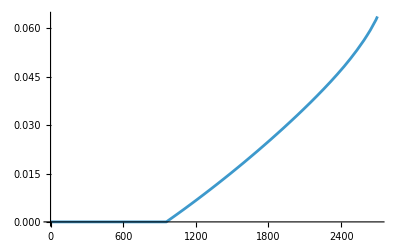

```mathematica
Plot[fprovaT4[x],{x,0,2700}]
```

```mathematica
fprovaP[x_]:=fFun[CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,4,2]],x,CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,5,2]]]
```

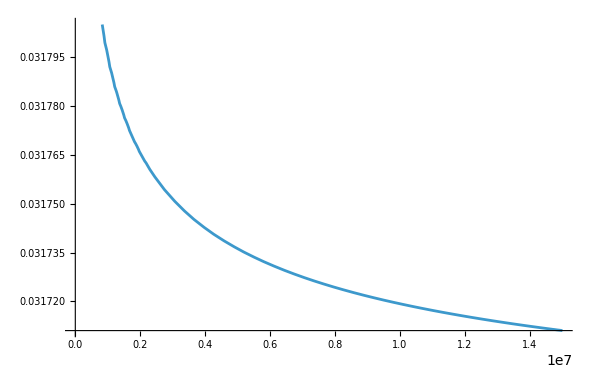

```mathematica
Plot[fprovaP[x],{x,0,15000000}]
```

```mathematica
fprovaT[x_]:=fFun[x,CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,4,1]],CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,5,2]]]
```

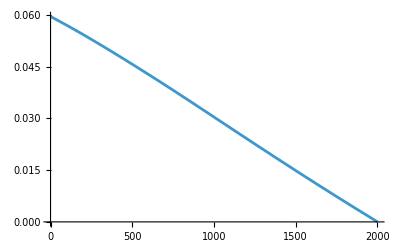

```mathematica
Plot[fprovaT[x],{x,0,2000}]
```

## Carpet Plot

### Range OUT COMPRESSIONE

```mathematica
βc=10.;
BPR=0.1;
```

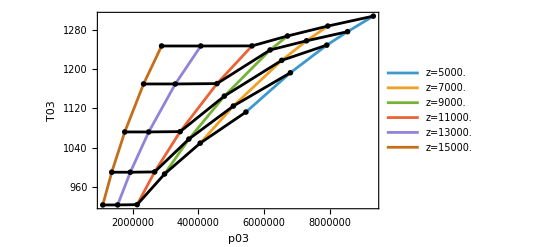

```mathematica
TFcomp[Ma_,z_]:=Module[{p03,T03},
{p03,T03}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[1,4,{1,2}]];
	Return[{p03,T03}]]

MaMin=0.8;
MaMax=1.6;

zMin=5000.;
zMax=15000.;
plotConstZ=ListLinePlot[Table[TFcomp[Ma,z],{z,zMin,zMax,2000},{Ma,MaMin,MaMax,0.2}],PlotLegends->Table["z="<>ToString[z],{z,zMin,zMax,2000}]];
plotConstMa=ListLinePlot[Table[TFcomp[Ma,z],{Ma,MaMin,MaMax,0.2},{z,zMin,zMax,2000}],PlotStyle->Black,PlotMarkers->Table[Ma,{Ma,MaMin,MaMax,0.2}]];
Show[plotConstZ,plotConstMa,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"p03","T03"}]
```

### 3 – 4: Subsonic Cruise Climb

```mathematica
Ma=0.8;
z=10364.7;
```

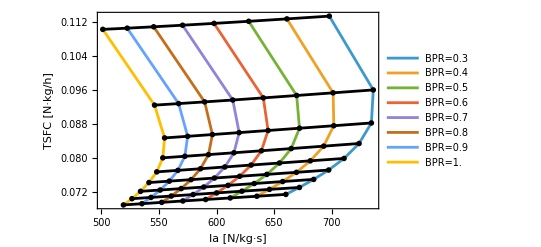

```mathematica
TFperf[βc_,BPR_]:=Module[{Ia,TSFC},
{Ia,TSFC}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[4,1;;2]];
Return[{Ia,TSFC}]]

βcmin=2;
βcmax=10;

BPRmin=0.3;
BPRmax=1;
plotConstBPR=ListLinePlot[Table[TFperf[βc,BPR],{BPR,BPRmin,BPRmax,0.1},{βc,βcmin,βcmax,1}],PlotLegends->Table["BPR="<>ToString[BPR],{BPR,BPRmin,BPRmax,0.1}]];
plotConstBeta=ListLinePlot[Table[TFperf[βc,BPR],{βc,βcmin,βcmax,1},{BPR,BPRmin,BPRmax,0.1}],PlotStyle->Black,PlotMarkers->Table[βc,{βc,βcmin,βcmax,1}]];
Show[plotConstBPR,plotConstBeta,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Ia [N/kg·s]","TSFC [N·kg/h]"}]
```

### 6 – 7: Supersonic penetration – PENETRATION

```mathematica
Ma=1.6;
z=10000.;
```

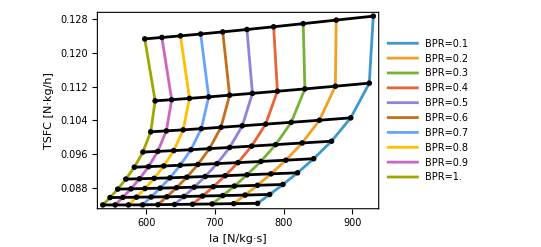

```mathematica
TFperf[βc_,BPR_]:=Module[{Ia,TSFC},
{Ia,TSFC}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[4,1;;2]];
Return[{Ia,TSFC}]]

βcmin=2;
βcmax=10;

BPRmin=0.1;
BPRmax=1;
plotConstBPR=ListLinePlot[Table[TFperf[βc,BPR],{BPR,BPRmin,BPRmax,0.1},{βc,βcmin,βcmax,1}],PlotLegends->Table["BPR="<>ToString[BPR],{BPR,BPRmin,BPRmax,0.1}]];
plotConstBeta=ListLinePlot[Table[TFperf[βc,BPR],{βc,βcmin,βcmax,1},{BPR,BPRmin,BPRmax,0.1}],PlotStyle->Black,PlotMarkers->Table[βc,{βc,βcmin,βcmax,1}]];
Show[plotConstBPR,plotConstBeta,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Ia [N/kg·s]","TSFC [N·kg/h]"}]
```

### 8 – 9: Escape Dash

```mathematica
Ma=1.4;
z=10000.;
```

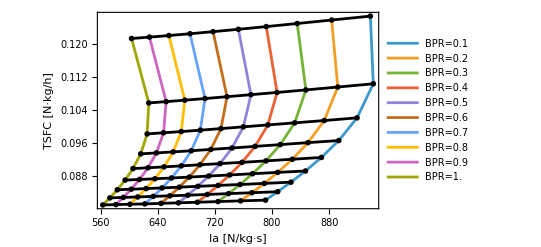

```mathematica
TFperf[βc_,BPR_]:=Module[{Ia,TSFC},
{Ia,TSFC}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[4,1;;2]];
Return[{Ia,TSFC}]]

βcmin=2;
βcmax=10;

BPRmin=0.1;
BPRmax=1;
plotConstBPR=ListLinePlot[Table[TFperf[βc,BPR],{BPR,BPRmin,BPRmax,0.1},{βc,βcmin,βcmax,1}],PlotLegends->Table["BPR="<>ToString[BPR],{BPR,BPRmin,BPRmax,0.1}]];
plotConstBeta=ListLinePlot[Table[TFperf[βc,BPR],{βc,βcmin,βcmax,1},{BPR,BPRmin,BPRmax,0.1}],PlotStyle->Black,PlotMarkers->Table[βc,{βc,βcmin,βcmax,1}]];
Show[plotConstBPR,plotConstBeta,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Ia [N/kg·s]","TSFC [N·kg/h]"}]
```

### 9 – 10: Subsonic Cruise Climb:

```mathematica
Ma=0.8;
z=12651.8;
```

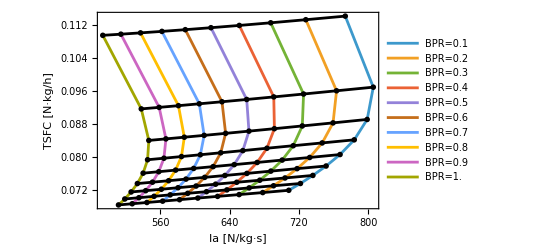

```mathematica
TFperf[βc_,BPR_]:=Module[{Ia,TSFC},
{Ia,TSFC}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[4,1;;2]];
Return[{Ia,TSFC}]]

βcmin=2;
βcmax=10;

BPRmin=0.1;
BPRmax=1;
plotConstBPR=ListLinePlot[Table[TFperf[βc,BPR],{BPR,BPRmin,BPRmax,0.1},{βc,βcmin,βcmax,1}],PlotLegends->Table["BPR="<>ToString[BPR],{BPR,BPRmin,BPRmax,0.1}]];
plotConstBeta=ListLinePlot[Table[TFperf[βc,BPR],{βc,βcmin,βcmax,1},{BPR,BPRmin,BPRmax,0.1}],PlotStyle->Black,PlotMarkers->Table[βc,{βc,βcmin,βcmax,1}]];
Show[plotConstBPR,plotConstBeta,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"Ia [N/kg·s]","TSFC [N·kg/h]"}]
```

### Range Beta

```mathematica
Ma=1.6;
z=5000.;
```

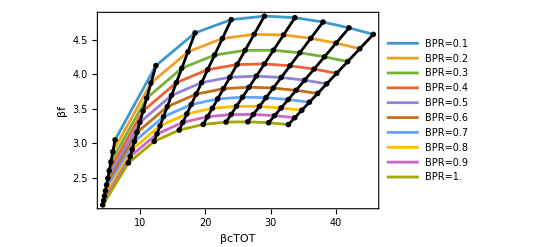

```mathematica
TFbeta[βc_,BPR_]:=Module[{βcTOT,βf},
{βcTOT,βf}=CalcTurboFanCycle[pythonExe,Ma,z,γair,Rair,ηd,ηpf,ηmf,BPR,ηpc,ηmc,βc,ϵ1,ϵ2,Qf,γgas,Rgas,ηb,ηab,ηpb,ηpab,T4max,TR,T7,ηpt,ηmt,ηn,JP8,oxid,False,"adapted","off","interpolation"][[5]];
Return[{βcTOT,βf}]]

βcmin=2;
βcmax=10;

BPRmin=0.1;
BPRmax=1;
plotConstBPR=ListLinePlot[Table[TFbeta[βc,BPR],{BPR,BPRmin,BPRmax,0.1},{βc,βcmin,βcmax,1}],PlotLegends->Table["BPR="<>ToString[BPR],{BPR,BPRmin,BPRmax,0.1}]];
plotConstBeta=ListLinePlot[Table[TFbeta[βc,BPR],{βc,βcmin,βcmax,1},{BPR,BPRmin,BPRmax,0.1}],PlotStyle->Black,PlotMarkers->Table[βc,{βc,βcmin,βcmax,1}]];
Show[plotConstBPR,plotConstBeta,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"βcTOT","βf"}]
```

## Low Pressure Compressor Sizing

## Mean Line Analysis

```mathematica
(* From cycle computations *)
T0inletLPC=corePointsTF[[2,2]];
p0inletLPC=corePointsTF[[2,1]];
βf=betaTF[[2]];
cpAir=cp[γair,Rair];
(*Aerodynamic design choices*)
α1=0;                                                (* α1=0 perché non vogliamo avere l'IGV *)
DF= 0.58;                                       (* Fattore di Diffusione: misura quanto il flusso rallenta e devia in una paletta; pag 301 Marcocci *)
σLPC=0.8;                                     (* Solidità della paletta: indica quanto è fitta la schiera di palette; pag 307 Marcocci *)
desiredΔT0stage=50;             (* Salto di temperatura desiderato per stadio; pag 307 Marcocci *)
massflowLPC= 1+BPR+ϵ1+ϵ2; (* CAMBIARE, NON CORRETTO *)
(*Structural design choices*)
σmaterial=344700000;         (* Sforzo ammissibile del disco rotante del compressore *)
ρblade=4680;                            (* Densità delle palette realizzate in leghe di titanio *)
taper=0.8;                                (* Fattore adimenisonale che rappresenta quanto la sezione della pala o del disco cambia lungo il raggio; pag 310 Marcocci *)
```

With given conditions, #Stages = 5 with ΔT0_stage = 46.8801

Compressor efficiency = 0.868722 with ΔT0_comp = 234.401

T0in = 337.557 :: T0out = 571.958

p0in = 99604.5 :: p0out = 519729.

Wheelspeed = 8364.07 rad/s

rmean = 0.0180098

Stage # 1 Pratio = 1.50365 p0out = 149770. T0out = 384.437 Mout = 0.493817 α1 = 0 β2 = 0. Δβ = 38.4793

Stage # 2 Pratio = 1.43422 p0out = 214804. T0out = 431.317 Mout = 0.497713 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 3 Pratio = 1.38151 p0out = 296755. T0out = 478.198 Mout = 0.500828 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 4 Pratio = 1.34015 p0out = 397697. T0out = 525.078 Mout = 0.503374 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 5 Pratio = 1.30685 p0out = 519729. T0out = 571.958 Mout = 0.505496 α1 = 0. β2 = 0. Δβ = 38.4793

Database contains: T,T0,p,p0,s,rmean,rtip,rhub,CrossSection,M,Mrel

Triangle contains: α1,α2,β1,β2,Ca,U,Cu1,Cu2,Wu1,Wu2,ω

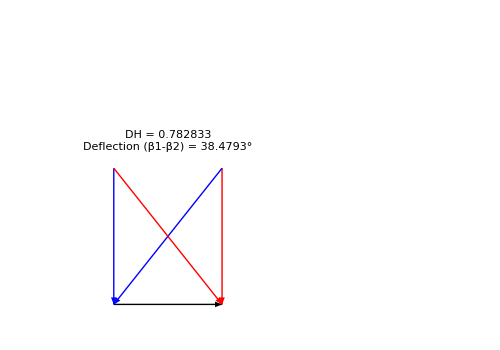

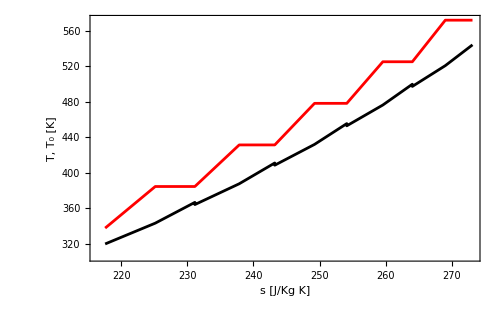

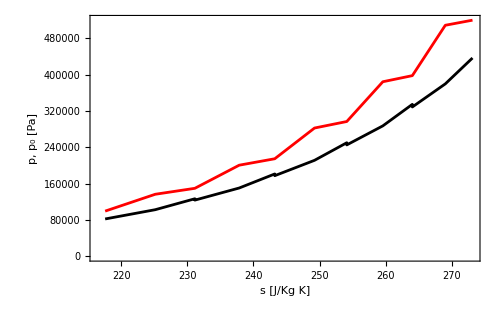

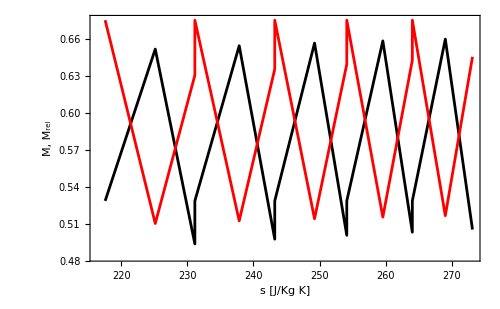

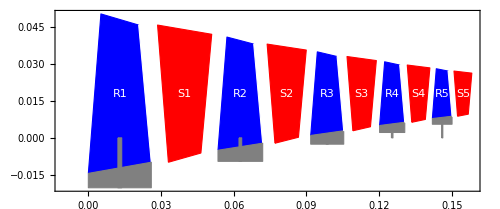

```mathematica
{nStagesLPC,allStagesLPC,saveTriangleLPC,plotLPC}=designFullCompressorUpdated[pythonExe,T0inletLPC,p0inletLPC,βf,ηpf,γair,Rair,cpAir,α1,DF,σLPC,desiredΔT0stage,massflowLPC,σmaterial,ρblade,taper];
plotLPC
nicePlotFromDB[allStagesLPC,5,1,2,"s [J/Kg K]","T, T_0 [K]"]
nicePlotFromDB[allStagesLPC,5,3,4,"s [J/Kg K]","p, p_0 [Pa]"]
nicePlotFromDB[allStagesLPC,5,10,11,"s [J/Kg K]","M, M_rel"]
drawCompressor[allStagesLPC,7,8,nStagesLPC]
```

## Properties Across Stage along Mean Path Line

```mathematica
collectCompressorGeometries[allStagesLPC,saveTriangleLPC,nStagesLPC,massflowLPC,Rair]
```

Parametro | Valore
Aree delle sezioni (m.b2) | {0.00735018,0.00521664,0.00385265,0.00293636,0.00229595}
Raggi medi (m) | {0.0180098,0.0180098,0.0180098,0.0180098,0.0180098}
Diametri medi (m) | {0.0360196,0.0360196,0.0360196,0.0360196,0.0360196}
Raggi bordo esterno - tip (m) | {0.050487,0.0410599,0.035033,0.0309843,0.0281546}
Raggi bordo interno - root (m) | {-0.0144674,-0.00504024,0.000986642,0.00503532,0.00786501}
Angolo medio α1 (rad) | {0.,0.,0.,0.,0.}
Angolo medio β2 (rad) | {0.,0.,0.,0.,0.}
Rapporto velocità assiale/periferica φ  | {1.2581,1.2581,1.2581,1.2581,1.2581}
Velocità rotazione (RPM) | 1584.41
Portata massica ridotta media (kg/s) | 0.531432

## High Pressure Compressor Sizing

## Mean Line Analysis

```mathematica
(* From cycle computations *)
T0inletHPC=corePointsTF[[3,2]];
p0inletHPC=corePointsTF[[3,1]];
cpAir=cp[γair,Rair];
(*Aerodynamic design choices*)
α1=0;                                                (* α1=0 perché non vogliamo avere l'IGV *)
DF= 0.58;                                       (* Fattore di Diffusione: misura quanto il flusso rallenta e devia in una paletta; pag 301 Marcocci *)
σHPC=1.1;                                     (* Solidità della paletta: indica quanto è fitta la schiera di palette; pag 307 Marcocci *)
desiredΔT0stage=50;             (* Salto di temperatura desiderato per stadio; pag 307 Marcocci *)
massflowHPC= 1+ϵ1+ϵ2;  (* CAMBIARE, NON CORRETTO *)
(*Structural design choices*)
σmaterial=344700000;         (* Sforzo ammissibile del disco rotante del compressore *)
ρblade=4680;                            (* Densità delle palette realizzate in leghe di titanio *)
taper=0.8;                                (* Fattore adimenisonale che rappresenta quanto la sezione della pala o del disco cambia lungo il raggio; pag 310 Marcocci *)
```

With given conditions, #Stages = 13 with ΔT0_stage = 47.3414

Compressor efficiency = 0.867576 with ΔT0_comp = 615.439

T0in = 573.699 :: T0out = 1189.14

p0in = 519729. :: p0out = 5.19729×10^6

Wheelspeed = 17445.7 rad/s

rmean = 0.0112566

Stage # 1 Pratio = 1.28497 p0out = 667837. T0out = 621.04 Mout = 0.507153 α1 = 0 β2 = 0. Δβ = 38.4793

Stage # 2 Pratio = 1.26143 p0out = 842428. T0out = 668.381 Mout = 0.50871 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 3 Pratio = 1.24146 p0out = 1.04584×10^6 T0out = 715.723 Mout = 0.510057 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 4 Pratio = 1.22433 p0out = 1.28045×10^6 T0out = 763.064 Mout = 0.511235 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 5 Pratio = 1.20945 p0out = 1.54865×10^6 T0out = 810.406 Mout = 0.512273 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 6 Pratio = 1.19643 p0out = 1.85285×10^6 T0out = 857.747 Mout = 0.513196 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 7 Pratio = 1.18492 p0out = 2.19548×10^6 T0out = 905.089 Mout = 0.514021 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 8 Pratio = 1.17469 p0out = 2.579×10^6 T0out = 952.43 Mout = 0.514763 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 9 Pratio = 1.16553 p0out = 3.00589×10^6 T0out = 999.771 Mout = 0.515433 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 10 Pratio = 1.15728 p0out = 3.47865×10^6 T0out = 1047.11 Mout = 0.516043 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 11 Pratio = 1.14981 p0out = 3.99978×10^6 T0out = 1094.45 Mout = 0.516599 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 12 Pratio = 1.14302 p0out = 4.57181×10^6 T0out = 1141.8 Mout = 0.517109 α1 = 0. β2 = 0. Δβ = 38.4793

Stage # 13 Pratio = 1.13681 p0out = 5.19729×10^6 T0out = 1189.14 Mout = 0.517578 α1 = 0. β2 = 0. Δβ = 38.4793

Database contains: T,T0,p,p0,s,rmean,rtip,rhub,CrossSection,M,Mrel

Triangle contains: α1,α2,β1,β2,Ca,U,Cu1,Cu2,Wu1,Wu2,ω

-Graphics-

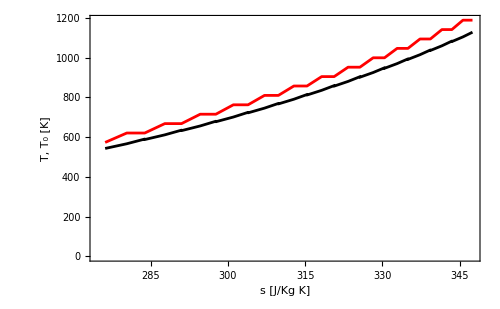

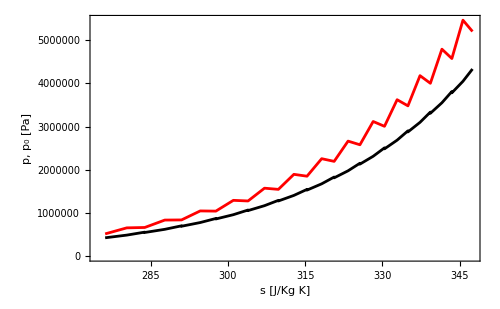

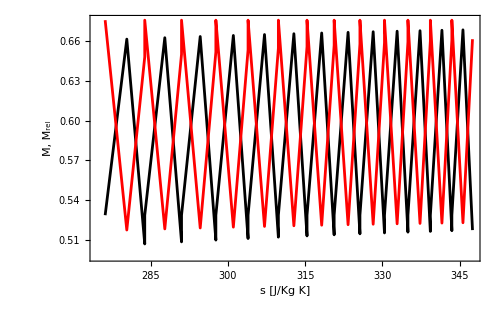

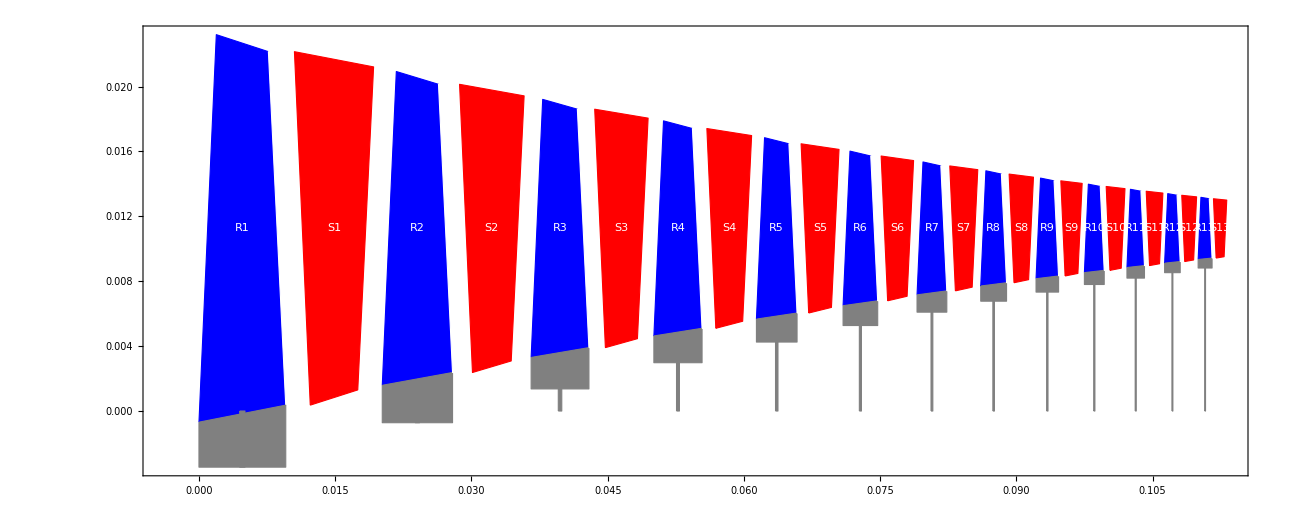

```mathematica
{nStagesHPC,allStagesHPC,saveTriangleHPC,plotHPC}=designFullCompressorUpdated[pythonExe,T0inletHPC,p0inletHPC,βc,ηpc,γair,Rair,cpAir,α1,DF,σHPC,desiredΔT0stage,massflowHPC,σmaterial,ρblade,taper];
plotHPC
nicePlotFromDB[allStagesHPC,5,1,2,"s [J/Kg K]","T, T_0 [K]"]
nicePlotFromDB[allStagesHPC,5,3,4,"s [J/Kg K]","p, p_0 [Pa]"]
nicePlotFromDB[allStagesHPC,5,10,11,"s [J/Kg K]","M, M_rel"]
drawCompressor[allStagesHPC,7,8,nStagesHPC]
```

## Properties Across Stage along Mean Path Line

```mathematica
collectCompressorGeometries[allStagesHPC,saveTriangleHPC,nStagesHPC,massflowHPC,Rair]
```

Parametro | Valore
Aree delle sezioni (m.b2) | {0.00168949,0.00136798,0.00112505,0.00093777,0.000790874,0.00067389,0.000579471,0.000502351,0.000438688,0.000385627,0.000341018,0.000303217,0.000270955}
Raggi medi (m) | {0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566,0.0112566}
Diametri medi (m) | {0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132,0.0225132}
Raggi bordo esterno - tip (m) | {0.0232003,0.0209274,0.01921,0.0178861,0.0168476,0.0160206,0.0153531,0.0148079,0.0143578,0.0139827,0.0136674,0.0134001,0.0131721}
Raggi bordo interno - root (m) | {-0.000687144,0.00158575,0.00330316,0.00462709,0.00566556,0.00649257,0.00716006,0.00770525,0.00815531,0.00853042,0.00884578,0.00911301,0.00934109}
Angolo medio α1 (rad) | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
Angolo medio β2 (rad) | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
Rapporto velocità assiale/periferica φ  | {1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581,1.2581}
Velocità rotazione (RPM) | 3835.
Portata massica ridotta media (kg/s) | 0.531432

## High Pressure Turbine Sizing

### Cycle Data

```mathematica
T0inletHPT=corePointsTF[[5,2]];
p0inletHPT=corePointsTF[[5,1]];
T0outletHPT=corePointsTF[[6,2]];
cpTurbHPT=cpBFun[corePointsTF[[4,2]],corePointsTF[[4,1]],corePointsTF[[5,2]]];
```

### Design choice on rotational speed (to be checked with structural calculations, then iterated)

Attualmente, non sono disponibili dati pubblici specifici sulla velocità periferica U (in m/s) della turbina ad alta pressione (HPT) del motore EJ200 dell’Eurofighter Typhoon. Tuttavia, è possibile stimare questo valore utilizzando informazioni note e formule ingegneristiche standard. 
Dal NASA Technical Memorandum 4140, il motore General Electric F404, utilizzato in aerei come l’F/A-18 Hornet, ha una velocità dell’albero ad alta pressione di circa 14.000 RPM. Pertanto, è ragionevole supporre che l’EJ200 operi in un intervallo simile. 
Anche se non sono disponibili dati specifici sul raggio medio della turbina ad alta pressione dell’EJ200, possiamo fare una stima basata sulle dimensioni complessive del motore e su analogie con motori simili. L’EJ200 ha un diametro esterno di circa 0,74 metri. Considerando lo spessore delle pareti e altri componenti, il raggio medio della turbina ad alta pressione potrebbe essere stimato intorno a 0,15 metri. 
Per cui si ottiene una stima intorno a 235,6 m/s.

```mathematica
UTurbHPT=450;
```

### Automated Procedure

```mathematica
PsiTurb[T0inletHPT-T0outletHPT,UTurbHPT,cpTurbHPT] (* Carico di stadio adimensionale, rappresenta il lavoro specifico fornito dal fluido alla turbina *)
```

4.62796

```mathematica
SizeTurbine[T0inletHPT,T0outletHPT,p0inletHPT,UTurbHPT,cpTurbHPT,γgas,"HPT","off"];
```

TURBINE DESIGN PARAMETERS

Number of stages = 4

Stage loadings (ψ) = 1.15699

========================================

stage #1

Stage inlet conditions: T0in = 2000. K, p0in = 2.46871×10^6 Pa

M2 = 1., M3R = 0.8, U = 450

Target τ = 0.912216

Temperature ratio (τ) | 0.912216
Reaction degree (R) | 0.178347
Flow angles (α2, β2, α3, β3) | {46.4388,16.7264,-10.349,29.6138}
Turning | 46.3402
Axial velocity (Ca) | 599.191
Mach numbers (M2, M2R, M3, M3R) | {1.,0.719574,0.707002,0.8}

========================================

stage #2

Stage inlet conditions: T0in = 1824.43 K, p0in = 1.70472×10^6 Pa

M2 = 0.9, M3R = 0.8, U = 450

Target τ = 0.903769

Temperature ratio (τ) | 0.903769
Reaction degree (R) | 0.342672
Flow angles (α2, β2, α3, β3) | {47.2218,11.6525,-3.9437,38.8535}
Turning | 50.5061
Axial velocity (Ca) | 514.58
Mach numbers (M2, M2R, M3, M3R) | {0.9,0.624109,0.624481,0.8}

========================================

stage #3

Stage inlet conditions: T0in = 1648.87 K, p0in = 1.13384×10^6 Pa

M2 = 0.9, M3R = 0.8, U = 450

Target τ = 0.893523

Temperature ratio (τ) | 0.893523
Reaction degree (R) | 0.355233
Flow angles (α2, β2, α3, β3) | {49.8385,12.2034,-3.67318,42.1289}
Turning | 54.3323
Axial velocity (Ca) | 464.548
Mach numbers (M2, M2R, M3, M3R) | {0.9,0.59387,0.594531,0.8}

========================================

stage #4

Stage inlet conditions: T0in = 1473.3 K, p0in = 720263. Pa

M2 = 0.9, M3R = 0.8, U = 450

Target τ = 0.880834

Temperature ratio (τ) | 0.880834
Reaction degree (R) | 0.367793
Flow angles (α2, β2, α3, β3) | {53.1474,13.0719,-3.38737,46.2001}
Turning | 59.272
Axial velocity (Ca) | 408.354
Mach numbers (M2, M2R, M3, M3R) | {0.9,0.554141,0.554682,0.8}

## Low Pressure Turbine Sizing

### Cycle Data

```mathematica
T0inletLPT=corePointsTF[[6,2]];
p0inletLPT=corePointsTF[[6,1]];
T0outletLPT=corePointsTF[[7,2]];
cpTurbLPT=cpBFun[corePointsTF[[4,2]],corePointsTF[[4,1]],corePointsTF[[5,2]]];;
```

### Design choice on rotational speed (to be checked with structural calculations, then iterated)

```mathematica
UTurbLPT=450.;
```

### Automated Procedure

```mathematica
PsiTurb[T0inletLPT-T0outletLPT,UTurbLPT,cpTurbLPT]
```

1.44301

```mathematica
SizeTurbine[T0inletLPT,T0outletLPT,p0inletLPT,UTurbLPT,cpTurbLPT,γgas,"LPT","off"];
```

TURBINE DESIGN PARAMETERS

Number of stages = 2

Stage loadings (ψ) = 0.721507

========================================

stage #1

Stage inlet conditions: T0in = 1297.73 K, p0in = 519729. Pa

M2 = 1., M3R = 0.8, U = 450.

Target τ = 0.915634

Temperature ratio (τ) | 0.915634
Reaction degree (R) | 0.236251
Flow angles (α2, β2, α3, β3) | {46.2603,6.59971,-20.5309,29.0211}
Turning | 35.6208
Axial velocity (Ca) | 484.24
Mach numbers (M2, M2R, M3, M3R) | {1.,0.695995,0.747,0.8}

========================================

stage #2

Stage inlet conditions: T0in = 1188.25 K, p0in = 364337. Pa

M2 = 0.9, M3R = 0.8, U = 450.

Target τ = 0.90786

Temperature ratio (τ) | 0.90786
Reaction degree (R) | 0.371031
Flow angles (α2, β2, α3, β3) | {46.7506,-0.632455,-16.0711,38.1675}
Turning | 37.5351
Axial velocity (Ca) | 418.958
Mach numbers (M2, M2R, M3, M3R) | {0.9,0.616695,0.654546,0.8}